# Mathematica Advanced Lesson 17 Dynamic Interaction Dr. Dale R. Doty University of Tulsa

## Introduction to Dynamic Programming:

## Dynamic[ ... ]

### Background

```mathematica
Clear["Global`*"]
```

Dynamic[expr]

Note the distinction between

              internal value of  expr like:   Integrate[f,x]

              front end display of  expr like:  ∫fⅆx

Note the distinction between

              internal  value of  expr like:   Plot[Sin[x],{x,0,2π}]
              front end display of  expr like:

### Dynamic connections are by default bi-directional between value and display. Illustration: Change Dynamic value → to generate a change in its Dynamic display.

Evaluate:

```mathematica
Clear[f,g,x,y];

Dynamic[Integrate[f[x],x]]
```

Change Dynamic value → x = y  and look at what is displayed in the above Output Cell for Dynamic[Integrate[f[x],x]]:

```mathematica
x=y
```

Change Dynamic value → f=g  and look at what is displayed in the above Output Cell for Dynamic[Integrate[f[x],x]]:

```mathematica
f=g
```

Change Dynamic value → f=Sin  and look at what is displayed in the above Output Cell for Dynamic[Integrate[f[x],x]]:

```mathematica
f=Sin
```

Now if you have evaluated all of the above Input cells, you should see displayed -Cos[y] in the following Input Cell.

However, the internal value is actually Dynamic[Integrate[f[x],x]] as shown below with InputForm:

```mathematica
//InputForm
```

Change Dynamic value → f=g  and look at what happens in the above Input Cell that WAS displayed as -Cos[y]:

```mathematica
f=g
```

### Dynamic connections are by default bi-directional between value and display.

Illustration:  Slider2D[...] 

You MUST ALWAYS keep in mind the distinction between Dynamic value and display.

Note the correspondence between Dynamic Value Input Cell and Dynamic Value Output Cell.

Note the correspondence between Dynamic Display Input Cell and Dynamic Display Output Cell.

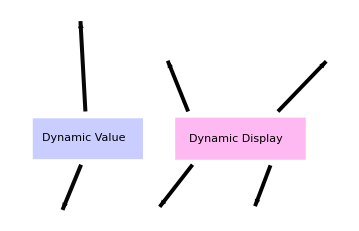

Illustration Code: 

	Evaluate the following normal Input Cell and move the Dynamic Slider[...] in the Output Cell:

```mathematica
xxx=.2;
yyy=.3;

{
Slider2D[
{
Dynamic[xxx],
Dynamic[yyy]
}
],
Row[{"xxx = ",Dynamic[xxx],"  and  yyy = ",Dynamic[yyy]}]
}
```

Illustration: Evaluate the following normal Input Cell that contains both non-Dynamic and Dynamic content.

Evaluate:

```mathematica
Clear[f,x];

{  ∫f[x]ⅆx,   Dynamic[∫f[x]ⅆx]  }
```

First, observe that both the non-Dynamic and Dynamic content are displayed the same.

Illustration: Part 1: 

Now change both the f and x for the non-Dynamic ∫f[x]ⅆx on the left side of the above Output Cell (NOT the Input Cell above it)!

Note that a normal (non-Dynamic) Output Cell (when edited) changes into an Input Cell containing the changes.

Illustration: Part 2: Try unsuccessfully to change Dynamic display → to generate a change in its Dynamic value.

Now TRY unsuccessfully to change either the f or x for the Dynamic display ∫f[x]ⅆx on the right side of the above Cell that contains the changes from Part 1 (the bottom not the top of the two cells)!

The edit is prohibited!

Dynamic connections are by default bi-directional between value and display.

Most Dynamic displays do NOT have a REVERSIBLE link to the underlying Dynamic value and therefore the edit will be prohibited.

### So what Dynamic displays are REVERSIBLE? Such displays can be edited and can establish a bi-directional link between value and display. Illustration: A low level bi-directional command: Slider[...] (bi-directional link between value and display)

Evaluate and move the Slider[...] to see the Dynamic change in xx:

```mathematica
xx=0.4;

{
Slider[Dynamic[xx]],

Dynamic[xx]
}
```

### So what other Dynamic displays are REVERSIBLE? Such displays can be edited and can establish a bi-directional link between value and display. Illustration: Some low level bi-directional commands: Slider[...] (bi-directional link between value and display) SetterBar[...] (bi-directional link between value and display) Slider2D[...] (bi-directional link between value and display) Locator[...] (bi-directional link in Graphics to Graphics value and display) (Graphic Primative) LocatorPane[...](bi-directional link in Graphics to Graphics value and display) (Intermediate Graphic) ColorSlider[...] (bi-directional link between value and color display) ActionMenu[...](bi-directional link between value and display) PopupMenu[...](bi-directional link between value and display) RadioButtonBar[...](bi-directional link between value and display) CheckboxBar[...](bi-directional link between value and display) InputField[...] (bi-directional link between value and display)

Evaluate the following Cell and change the resulting controls for EACH and EVERY control:

```mathematica
Clear[f,t,x,y];
xx=.2;
yy=.3;
zz=.5;
color=RGBColor[xx,yy,zz];

Partition[
{
Slider[Dynamic[xx]],
SetterBar[Dynamic[xx],Range[0,1,0.2]],
Slider2D[{Dynamic[xx],Dynamic[yy]}],
Graphics[
{
Red,Disk[{1/2,1/2},{Dynamic[xx/3],Dynamic[yy/3]}],
Thick,Black,Line[{{1/2,1/2},Dynamic[{xx,yy}]}],
PointSize[0.05],Point[{1/2,1/2}],
Locator[Dynamic[{xx,yy}]]
},
PlotRange->{{0,1},{0,1}},
ImageSize->200,
AspectRatio->0.4
],
LocatorPane[Dynamic[{xx,yy}],Plot[Sin[2π tt],{tt,0,1},PlotLabel->"LocatorPane[...]"]],
Row[{ColorSlider[Dynamic[color,(color=#;xx=color_⟦2⟧;yy=color_⟦1⟧)&],AppearanceElements->"Spectrum"],Graphics[{RGBColor[Dynamic[yy],Dynamic[xx],Dynamic[color_⟦3⟧]],Disk[]},ImageSize->50]}],
ActionMenu[Row[{"ActionMenu[...]\nxx = ",Dynamic[xx]}],{"Choose: xx = 0.0":>(xx=0.0),"Choose: xx = 0.2":>(xx=0.2),"Choose: xx = 0.4":>(xx=.4),"Choose: xx = 0.6":>(xx=.6),"Choose: xx = 0.8":>(xx=.8),"Choose: xx = 1.0":>(xx=1.0)}],
RadioButtonBar[Dynamic[xx],{0.0->".0",.2->".2",.4->".4",.6->".6",.8->".8",1.->"1."}],
PopupMenu[Dynamic[xx],{0.0,0.2,0.4,0.6,0.8,1.0},Dynamic[xx]],
Panel[{"Type in a number between 0. and 1. in the \nInputField[...] box and press the Enter key:",InputField[Dynamic[xx]]}//Column,FrameMargins->5],
Row[{"\n{xx,yy} = ",{Dynamic[Round[xx,.001]],Dynamic[Round[yy,.001]]}}],
Row[{"\n",∫_Dynamic[Round[xx,.001]]^Dynamic[Round[yy,.001]] "Sin"[t]ⅆt," = ",Dynamic[Round[∫_xx^yy Sin[t]ⅆt,.001]]}]
},
2]//Grid
```

### Where do you place Dynamic[display] to have a change in Dynamic value → generate a change in the Dynamic display.

Almost anywhere!

In the following example, Dynamic surrounds all of expr = Plot3D[...] and it works!

```mathematica
DynamicModule[{x=2,y=2},
Column[{
Slider[Dynamic[x],{1,5}],
Slider[Dynamic[y],{1,5}],
Dynamic[
Plot3D[Sin[xx*yy],{xx,0,x},{yy,0,y},PlotLabel->"Dynamic[Plot3D[...]] works!"]
]
}]
]
```

As long as the expression SURROUNDING Dynamic[expr]has sufficient information to evaluate properly, then it will work.

In the following example, Dynamic surrounds only x and y inside Plot3D[...]: 

	Plot3D[...Dynamic[x] ... Dynamic[y]...]  
	
and it only works half way!

```mathematica
DynamicModule[
{x=2,y=2},
Column[{
Slider[Dynamic[x],{1,2π}],
Slider[Dynamic[y],{1,2π}],
Plot3D[
Sin[xx*yy],
{xx,0,Dynamic[x]},
{yy,0,Dynamic[y]}
]
}]
]
```

Read the above error message and move the sliders and note that Plot3D[...] is trying to evaluate BEFORE the values from Dynamic[x] and Dynamic[y] have been supplied to Plot3D[...] in numeric form from the sliders.

	Plot3D::"plln": "Limiting value  in {xx,0,} is not a machine-size real number."

Plot3D[...] needs numeric information for the local variable x$87 that Plot3D made from Dynamic[x] in 

	{xx, 0, Dynamic[x]}
	{yy, 0, Dynamic[y]}

When you look above (before you moved the slider, the values were both 2), you see what appears to be OK:

	Plot3D[Sin[xx yy], {xx,0,2},{yy,0,2}]
	
but if you cut and paste this elsewhere into your notebook, you will see that the real content is:

	Plot3D[Sin[xx yy], {xx,0,x$$},{yy,0,y$$}]
	
and you will note that x$$ and y$$ do NOT have the value 2 at the time that Plot3D[...] was evaluated.
	
You might think that you can fix this problem in the usual way by surrounding the needed limits with Evaluate[Dynamic[x]] and Evaluate[Dynamic[y]].
This solves the evaluation problem, but will not solve the dynamic timing problem.

The observation that you need to make here is that the use of:

	Dynamic[...]
	
affects BOTH the evaluation process and the timing when a Cell is evaluated.

### Where do you place Dynamic[value] to have a change in Dynamic display → generate a change in the Dynamic value.

When used to assign values to expr through interactive operations, the expression in Dynamic[expr] will most often be a symbol x, an object x[i], a part e[[i]] or a list {x,y,…}. 

If expr in Dynamic[expr] is more complicated than what is given in the sentence above, then the link needed to create a change in the Dynamic value will be broken. Note that this is a very short list of acceptable options.

In the following example Dynamic surrounds a symbol

	Dynamic[xxx],

	Dynamic[yyy]
	
and it works:

```mathematica
xxx=.2;
yyy=.3;

{
Slider2D[
{
Dynamic[xxx],
Dynamic[yyy]
}
],
Row[{"xxx = ",Dynamic[xxx],"  and  yyy = ",Dynamic[yyy]}]
}
```

In the following example Dynamic surrounds a List

	Dynamic[{xxx, yyy}]
	
and it works:

```mathematica
xxx=.2;
yyy=.3;

{
Slider2D[
Dynamic[{xxx,yyy}]
],
Row[{"xxx = ",Dynamic[xxx],"  and  yyy = ",Dynamic[yyy]}]
}
```

In the following example Dynamic surrounds a List with objects xxxx[i]

	Dynamic[{xxxx[1], xxxx[2]}]
	
and it works:

```mathematica
xxxx[1]=.2;
xxxx[2]=.3;

{
Slider2D[
Dynamic[{xxxx[1],xxxx[2]}]
],
Row[{"xxxx[1] = ",Dynamic[xxxx[1]],"  and  xxxx[2] = ",Dynamic[xxxx[2]]}]
}
```

In the following example Dynamic surrounds a function with any head (e.g. f) other than List

	Dynamic[f[xxx, yyy]]
	
and it does NOT work!

The link between Dynamic display needed to create a change in the Dynamic value is broken.

```mathematica
xxx=.2;
yyy=.3;

{
Slider2D[
Dynamic[f[xxx,yyy]]
],
Row[{"xxx = ",Dynamic[xxx],"  and  yyy = ",Dynamic[yyy]}]
}
```

In the following example, the Locator[Dynamic[...]] in graph on the left works. 

However in the right graph, Dynamic[...] is not close enough to symbol p (that contains a List) for the graphic Locator[...] to work.

The link between Dynamic display needed to create a change in the Dynamic value is broken for the plot on the right.

```mathematica
Row[{
DynamicModule[
{p={0,0}},
Framed[
Graphics[{Locator[Dynamic[p]]},PlotRange->1,ImageSize->200,PlotLabel->Row[{"Move the graphic Locator[...]\nLocator[Dynamic[p]] works!\n",Dynamic[p]}]]
]
],
DynamicModule[
{p={0,0}},Framed[Graphics[{Dynamic[Locator[p]]},PlotRange->1,ImageSize->200,PlotLabel->Row[{"Move the graphic Locator[...]\nDynamic[Locator[p]] does NOT work!\n",Dynamic[p]}]]
]
]
}]
```

### Dynamic[expr,...] 2nd argument to Dynamic

#### Dynamic[expr,f] Introduction

Dynamic[expr]
represents an object that displays as the dynamically updated current value of expr. If the displayed form of Dynamic[expr] is interactively changed or edited, an assignment expr=val is done to give expr the new value val that corresponds to the displayed form.  

Note: 

	By default, Dynamic[...] performs an assignment operation when used in interactive elements.

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[
Dynamic[x]
],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

Dynamic[expr,f]

                     Continually evaluatesf[val,expr]during interactive changing or editing of val.

By default, Dynamic[...] performs an assignment operation to expr when used in interactive elements.

	This is ONLY TRUE when Dynamic[...] has only ONE ARGUMENT!!

	This is NOT TRUE when Dynamic[...] has TWO ARGUMENTS!!
	
Example: Dynamic[...] has TWO ARGUMENTS:

	Dynamic[ x, Identity[#] & ]

	Note that x does NOT AUTOMATICALLY UPDATE!
	Therefore the Slider[...] can NOT EVEN MOVE!

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[

Dynamic[

x,

Identity[#]&

]

],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

Therefore, you MUST ALWAYS make the assignment explicitly, x=#1, whenever Dynamic[...] has TWO arguments:

	Dynamic[ x, (x=#1;Identity[#1])& ]

 	Now the Slider[...] both moves and updates x:

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[

Dynamic[

x,

(
x=#;
Identity[#]
)&

]

],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

When might it be necessary to require assignment by using the 2nd argument?
Example: If you want to compare the incoming value # to the outgoing value f.
The 2nd argument of Dynamic plots # and f first and then assigns f=# second.
Once the assignment has been made, the old value is gone.
I do not know any other way to do this using only one argument in Dynamic except to use the 2nd argument of Dynamic.
Click the following popup several times:

```mathematica
Clear[f,x,eee];

f=Sin[6x];

{
PopupMenu[

Dynamic[

f,

(
eee=Plot[Evaluate[{#,f}],{x,1,6},PlotLabel->Column[{Row[{"Incoming # = ",#}],Row[{"Outgoing f = ",f}]}]];
f=#
)&
],

{Sin[x],Cos[x],Log[x]}

],

Dynamic[eee]

}
```

#### Dynamic[expr,f]

Dynamic[expr,f]

                     Continually evaluatesf[val,expr]during interactive changing or editing of val

Example using the second argument of Dynamic[expr,f]:

Note:

	1: Evaluate the following Input Cell.
			 
	2: As you move the Slider[...], Dynamically change the size of the displayed x using the Dynamic value of x:
			 
			 f   is   (x=#;size=# 44+5)&
	
The code for Dynamic[expr,f]:

	Dynamic[ x, (x=#1;size=# 44+5)& ]

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[
Dynamic[
x,
(
x=#;
size=# 44+5
)&
]
],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

#### Dynamic[expr,{f,f_end}]

Dynamic[expr,{f,f_end}]
            also evaluates f_end[val,expr] when interactive changing or editing is complete. 

Example using the second argument of Dynamic[expr,{f,f_end}]:

Note:

	1: Evaluate the following Input Cell.
			 
	2: As you move the Slider[...], Dynamically change the size of the displayed x using the Dynamic value of x:
			 
			 f   is   (x=#;under=Sequence[ ];size=# 44+5)&
			 
	3: The instant you release your mouse button the displayed x is Underlined:
	
			f_end   is   (under=Underlined)&
	
The code for Dynamic[expr,{f,f_end}]:

	Dynamic[
x,
{
(x=#;under=Sequence[];size=# 44+5)&,
(under=Underlined)&
}
]

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[
Dynamic[
x,
{
(x=#;under=Sequence[];size=# 44+5)&,
(under=Underlined)&
}
]
],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

#### Dynamic[expr,{f_start,f,f_end}]

Dynamic[expr,{f_start,f,f_end}]
               also evaluates f_start[val,expr] when interactive changing or editing begins. 

Example using the second argument of Dynamic[expr,{f_start,f,f_end}]:

Note:

	1: Evaluate the following Input Cell.

	2: Before you press your mouse button on the Slider[....] observe that there is 
	    NO text Background color.
	
	3: The instant you press your mouse button a text background color appears set by:
	
			 f_start   is   (back=Hue[#])&  where  x=0.4
			 
	4: As you move the Slider[...], Dynamically change both the size and the background color 
	    of the displayed x using the Dynamic value of x:
			 
			 f   is   (x=#;under=Sequence[];size=# 44+5;back=Hue[#])&
			 
	5: The instant you release your mouse button the displayed x is Underlined:
	
			f_end   is   (under=Underlined)&
	
The code for Dynamic[expr,{f_start,f,f_end}]:

	Dynamic[
x,
{
(back=Hue[#])&,
(x=#;under=Sequence[];size=# 44+5;back=Hue[#])&,
(under=Underlined)&
}
]

```mathematica
Clear[f];
x=0.4;
size=14;
back=RGBColor[1,1,1];
under=Sequence[];

{
Slider[
Dynamic[
x,
{
(back=Hue[#])&,
(x=#;under=Sequence[];size=# 44+5;back=Hue[#])&,
(under=Underlined)&
}
]
],

Panel[Dynamic[Style[x,FontSize->size,Background->back,under]]]
}
```

### Dynamic[expr] Examples

#### Example: Dynamic and Slider2D

```mathematica
DynamicModule[
{p1={-1/2,-1/2},p2={0,1/2},p3={1/2,0}},
Panel[
Column[{
Framed[
Graphics[{Dynamic[Hue[Apply[Plus,p1+p2+p3]]],Polygon[{Dynamic[p1],Dynamic[p2],Dynamic[p3]}]},PlotRange->1,ImageSize->240]
],
Row[{
Slider2D[Dynamic[p1],{-1,1}],
" ",
Slider2D[Dynamic[p2],{-1,1}],
" ",
Slider2D[Dynamic[p3],{-1,1}]
}]
}]
]
]
```

#### Example: Constrain the coordinates of a point to lie on a circle: Click and drag point:

```mathematica
DynamicModule[
{p={0,1}},
LocatorPane[
Dynamic[p,(p=Normalize[#])&],
Graphics[
{Dashed,Circle[],PointSize[0.1],Point[Dynamic[p]]},
ImageSize->Tiny,
PlotRange->1.2
],
Appearance->None
]
]
```

#### Example: Construct a dynamic calculating interface:

```mathematica
DynamicModule[
{a=0,b=0,s={{5,30},{1,Infinity}}},

Deploy[
Style[
Panel[
Grid[
Transpose[
{
{Style["Input a number",Red],Style["Input another number",Red],"here is their sum","their difference","their product"},
{InputField[Dynamic[a],Number],InputField[Dynamic[b],Number],InputField[Dynamic[a+b],Enabled->False],InputField[Dynamic[a-b],Enabled->False],InputField[Dynamic[a b],Enabled->False]}}
],
Alignment->Right
],
ImageMargins->10
],
DefaultOptions->{InputField->{ContinuousAction->True,FieldSize->s}}
]
]
]
```

#### Example: Construct custom controls, i.e., an angular slider with range (-∞,∞): Click and Move Arrow to generate the number:

```mathematica
DynamicModule[
{angle=0,p={1,0},angleCalc},

{
LocatorPane[
Dynamic[p,(angleCalc@@Normalize/@{#,p})&],
Graphics[{Circle[],Arrowheads[0.15],Arrow[Dynamic[{{0,0},p}]]},ImageSize->Tiny],
Appearance->None
],
Panel[Dynamic[angle]]
},

Initialization:>(angleCalc[newp_,oldp_]:=(angle=angle+ArcCos[newp.oldp]Sign[Cross[newp].(newp-oldp)];p={Cos[angle],Sin[angle]}))
]
```

#### Example: Center a disk at mouse position as mouse moves over the graphics area:

```mathematica
Framed[
Graphics[
Disk[Dynamic[MousePosition[{"Graphics",Graphics},{0,0}]],0.2],
PlotRange->2,
ImageSize->Small
]
]
```

#### Example: Click several times within the framed area to see several bouncing balls:

```mathematica
Framed[
DynamicModule[
{contents={}},
EventHandler[
Graphics[
{PointSize[0.1],Point[Dynamic[contents=Map[If[#[[1,2]]≥0,{#[[1]]-#[[2]],#[[2]]+{0,0.001}},{{#[[1,1]],0},{1,-0.8}#[[2]]}]&,contents];Map[First,contents]]]},
PlotRange->{{0,1},{0,1}}
],

"MouseDown":>(AppendTo[contents,{MousePosition["Graphics"],{0,0}}])
]
]
]
```

## DynamicModule[ ... ]

```mathematica
Clear["Global`*"]
```

### Localizing and initializing Variables in Dynamic Output

DynamicModule[{x,y,…},expr]

  an object which maintains the same local instance of the symbols
 x,y,… in the course of all evaluations ofDynamicobjects in expr
  
  
DynamicModule[{x=x_0,y=y_0},expr]

  specifies initial values forx,y,…

DynamicModule has arguments identical to Module and is similarly used to localize and initialize variables, but there are important differences in how they operate.

You might be tempted to use Module in place of DynamicModule, and in fact this would appear to work at first. However, it is not a good idea for several reasons, which are discussed in more detail in "Advanced Dynamic Functionality".

DynamicModule does its work in the front end, not in the kernel. It remains unchanged by evaluation, and when formatted as output, it creates an invisible object embedded in the output expression which handles the localization. As long as that space of output remains in existence (e.g. is not deleted), the invisible object representing the DynamicModule will maintain the values of the variables, allowing them to be used in subsequent evaluations of Dynamic expressions within the scope (area) of the DynamicModule.

If you save a notebook containing a DynamicModule, close that notebook, then later reopen it in a new Mathematica session, the values of all the local variables will still be preserved and the sliders inside the DynamicModule will be in the same positions. This will not be the case with sliders linked to global variables (like the earliest examples in this tutorial), nor with sliders linked to variables localized with Module instead of DynamicModule. Such variables store their values in the current Mathematica kernel session, and they are lost as soon as you quit Mathematica.

In addition to localizing variables to particular regions of output, DynamicModule provides options to automatically initialize function definitions when an expression containing a DynamicModule is opened, and to clean up values when the expression is closed or deleted. More details are found in DynamicModule.

### Examples:

#### Interactive curve fit plot:

```mathematica
DynamicModule[
{pts={{0,0},{1,1},{2,0},{3,2}}},
LocatorPane[
Dynamic[pts],
Dynamic[
Plot[InterpolatingPolynomial[pts,x],{x,0,3},PlotRange->3]
]
]
]
```

#### Demonstate a sinusoidal relationship: Click and drag arrow:

```mathematica
angularSlider[Dynamic[angle_]]:=

DynamicModule[
{p={1,0},angleCalc},

LocatorPane[Dynamic[p,(angleCalc@@Normalize/@{#,p})&],Graphics[{Circle[],Arrowheads[0.15],Arrow[Dynamic[{{0,0},p}]]},ImageSize->Tiny],Appearance->None],

Initialization:>(angle=0;angleCalc[newp_,oldp_]:=(angle=angle+ArcCos[newp.oldp]Sign[Cross[newp].(newp-oldp)];p={Cos[angle],Sin[angle]}))
];

DynamicModule[
{θ=0},
Grid[
{
{angularSlider[Dynamic[θ]],Plot[Sin[x],{x,-10,10},Epilog->{PointSize[Medium],Dynamic@Point[{θ,Sin[θ]}]}]},
{ParametricPlot[{Cos[y],y},{y,-10,10},AspectRatio->2,Epilog->{PointSize[Medium],Dynamic@Point[{Cos[θ],θ}]}],{"θ = ",Dynamic[θ]," rad"}//Row}
}
]
]
```

## Manipulate[ ... ]: The Dynamic Function Used 95 % of the Time!

Manipulate[expr,{u,u_min,u_max}]
generates a version of expr with controls added to allow interactive 
manipulation of the value of u. 

Manipulate[expr,{u,u_min,u_max,du}]
allows the value of u to vary between u_min and u_max in steps du. 

Manipulate[expr,{{u,u_init},u_min,u_max,…}]
takes the initial value of u to be u_init. 

Manipulate[expr,{{u,u_init,u_lbl},…}]
labels the controls for u with u_lbl. 

Manipulate[expr,{u,{u_1,u_2,…}}]
allows u to take on discrete values u_1,u_2,…. 

Manipulate[expr,{u,…},{v,…},…]
provides controls to manipulate each of the u,v,…. 

Manipulate[expr,"c_u"->{u,…},"c_v"->{v,…},…]
links the controls to the specified controllers on an external device.

### Introduction to Manipulate[...]

The single command Manipulate lets you create an astonishing range of interactive applications with just a few lines of input. Manipulate is designed to be used by anyone who is comfortable using basic commands such as Table and Plot: it does not require learning any complicated new concepts, nor any understanding of user interface programing ideas.

The output you get from evaluating a Manipulate command is an interactive object containing one or more controls (sliders, etc.) that you can use to vary the value of one or more parameters. The output is very much like a small applet or widget: it is not just a static result, it is a running program you can interact with.

At its most basic, the syntax of Manipulate is identical to that of the humble function Table. 

Consider this Table command, which produces a list of numbers from 1 to 20 in steps of 1.

```mathematica
Table[n,{n,1,20,1}]
```

Simply replace the word Table with the word Manipulate, and you get an interactive application that lets you explore values of n from 1 to 20 in steps of 1 with a slider.

```mathematica
Manipulate[n,{n,1,20,1}]
```

Of course the whole point of Manipulate (and Table for that matter) is that you can put any expression you like in the first argument, not just a simple variable name. 

One way to think of Manipulate is as a way to interactively explore a large parameter space. You can move around that space at will, exploring interesting directions as they appear. 

Manipulate supports a wide range of alternate ways of specifying variables, which generate different kinds of controls for those variables. These dynamic controls include checkboxes, popup menus, and others in addition to sliders. 

The principle is that for each Dynamic variable, u, you ask for a particular set of possible values for the variable u (like from 1 to 20 in steps of 1 e.g. {u,1,20,1}) and Manipulate automatically chooses an appropriate type of control to make those values conveniently available.

	Possible Values:			Manipulate Automatically Chooses an Appropriate Type of Control:
	{u,u_min,u_max} |  			continuous manipulator (slider, animator, etc.)
	{u,u_min,u_max,du} |    			discrete manipulator with step du
	{u,{x_min,y_min},{x_max,y_max}}		2D slider
	{u,Locator}				a locator in a graphic
	{u,{u_1,u_2,…}}			setter bar for few elements; popup menu for more
	etc.					etc.
	etc.					etc.

Manipulate automatically wraps its first argument in Dynamic and passes the value of its TrackedSymbols option to a Refresh inside that. Everything to do with updating is handled by that Dynamic and Refresh.	 

A direct result for you is this: 
	If Manipulate[...]'s first argument is the ONLY Dynamic expr that you need to display and 
	ALL remaining arguments contain only Possible Values for controls (and annotations like " ... text ... ")
	(as illustrated in the following example with one expr and two controls and no annotations):

	Manipulate[
	
	  Plot[a x + b, {x, 0, 2Pi}] ,  ⟸ Dynamic expr[a, b] you want to control  
 	
	  {a, 0, 2} ,   ⟸ continuous Slider control of a from 0 to 2

	  {b, 1, 5, 1}	⟸ discrete Slider control of b from 1 to 5 in steps of 1

	]

	then Manipulate automatically handles ALL Dynamic issues and 
	you do NOT need to explicitly code a single Dynamic[...] expression yourself!

However, if there are additional Dynamic expressions in the remaining arguments to be used as Dynamic annotations, then you will need to program Dynamic[...] explicitly.

The output display generated by Manipulate[...] always contains two areas:

	Primary area for the Dynamic expression and
	Controls area.
	
By default the Output Cell generated from Manipulate[...] has the controls area is displayed on top and the primary area for the Dynamic expression displayed on the bottom. You can, of course, change this if you want.

For example:

	Manipulate[
	
	Plot[a x + b, {x, 0, 2Pi}],  ⟸ Dynamic expr displayed in the primary expression area
	
	{a, 0, 2} ,       ⟸ continuous Slider control of a from 0 to 2 displayed in the controls area
	Dynamic[ expr2 ] ,  ⟸ Dynamic expr you want to control displayed in the controls area
	... ,                 ⟸ other annotation to be displayed in the controls area
	{b, 1, 5, 1} ,   ⟸ discrete Slider control of b from 1 to 5 in steps of 1 displayed in the controls area
	... ,                 ⟸ other annotation to be displayed in the controls area
	Dynamic[ expr3 ] ,  ⟸ Dynamic expr you want to control displayed in the controls area
	... ,                 ⟸ other annotation to be displayed in the controls area
	{u,  ...  } ,       ⟸ control of u displayed in the controls area
	... ,                 ⟸ other annotation to be displayed in the controls area
	... ,                 ⟸ Dynamic expr you want to control displayed in the controls area
	...                   ⟸ more controls displayed in the controls area 
	 ] 

has a primary display area and many different controls and annotations in the controls area.

The primary display area for the Dynamic expression will always contain the expr in the first argument of 
	
	Manipulate[expr, ... ].  

There is in fact virtually no limit to what can be put into the controls area display
	
	Manipulate[expr, ... controls area ... ].  
	
These include arbitrary formatting constructs and dynamic objects, even controls that are not part of the Manipulate's control specifications. Anything placed in the variables sequence that is either a 

	string or 
	has head Dynamic, 
	Style, or 
	ExpressionCell
	... 
	
will automatically be interpreted as an annotation to be inserted into the controls area.

Manipulate supports a number of features that allow you to rearrange, annotate, and generally pretty up the displayed control area, to make it suit the needs of a particular example. 

Advanced users should remember, however, that Manipulate is by no means the only way to create interactive interfaces in Mathematica, and if you cannot do what you want using Manipulate, you can easily start using functions such as Dynamic and DynamicModule directly to create free-form, open-ended user interfaces not tied to the particular conventions of Manipulate.  

Manipulate supports the option SaveDefinitions->True, which causes it to automatically build into the Manipulate output a copy of all the definitions of functions referred to in the Manipulate input (and recursively any functions they refer to). These definitions are then reestablished when you start any new Mathematica sessions that the Manipulate output is opened in (even before the contents of the Manipulate are evaluated for the first time in the new session). 

Warning! If you delete all of your Output Cells when you close your Mathematica notebook session, then your will also delete the session information that you want to save.

You can use SaveDefinitions to store function definitions or datasets, but be warned that if you refer to a large volume of data, it will of course be present in the file containing the saved Manipulate output, potentially creating a very large file.

Manipulate does not precompute all the possible output values you could reach by moving its sliders: that would be completely impractical for all but the most trivial cases. That means it has to calculate, format, and display the current value in real time as each slider is being dragged. Obviously no matter how fast your computer, there is a limit to how much computation can be done in a reasonable amount of time, and if the expression you use in the first argument to Manipulate takes more than about a second to evaluate, you will not have a very satisfactory experience using Manipulate.

### MORE INFORMATION

The expression expr can be any graphic or other expression. 
If it is None, only the controls are displayed.

The following forms by default yield particular forms of controls:

| {u,u_min,u_max} | manipulator (slider, animator, etc.) 
       | {u,u_min,u_max,du} | discrete manipulator with step du 
       | {u,{x_min,y_min},{x_max,y_max}} | 2D slider
       | {u,Locator} | a locator in a graphic
       | {u,{u_1,u_2,…}} | setter bar for few elements; popup menu for more
       | {u,{True,False}} | checkbox
       | {u,color} | color slider
       | {u} | blank input field
       | {u,func} | create an arbitrary control from a function
       | {{u,u_init},…} | control with initial value u_init
       | {{u,u_init,u_lbl},…} | control with label u_lbl
       | {{u,…},…,opts} | control with particular options
       | Delimiter | horizontal delimiter
       | string, cell expression, etc. | explicit text, cell, etc. annotations

Possible annotations given in place of controls include expressions with heads: String, Style, Row, Item, Text, ExpressionCell, TextCell.

The label u_lbl for a control can be any expression.

The option setting ControlType->type attempts to use controls of the specified type.

Possible control types include: Animator, Checkbox, CheckboxBar, ColorSetter, ColorSlider, InputField, Manipulator, PopupMenu, RadioButton or RadioButtonBar, Setter or SetterBar, Slider, Slider2D, TogglerBar, Trigger and VerticalSlider. None can also be used.

ControlType options can be given separately for each variable. Options for the controls can also be given within the specification for the variables.

ControlType->Trigger specifies that a particular variable should be controlled by a trigger.

The control specification {u,u_min,u_max,…,Appearance->"Labeled"} yields a slider with value displayed as a label.

In the form {u,func}, Dynamic[u] is given as the first argument to func.

The form {u} is equivalent to {u, InputField}. 

{u, ColorSlider} gives a default color slider as a control.

In the form {u,Locator}, the value of u is a list giving x and y coordinates. The coordinates refer either to the first graphic in expr, or range from 0 to 1 in each direction across expr.

The form {{u,{{x_1,y_1},{x_2,y_2},…}},Locator} sets up a locator for each of the {x_i,y_i}, and makes the value of u be the list of all {x_i,y_i}.

The option setting LocatorAutoCreate->All specifies that new locators should be added for clicks that do not hit existing locators. Alt+Click deletes locators.

{{u,{}},Locator,LocatorAutoCreate->All} starts with no locators, but allows locators to be created.

If a variable u is used more than once, linked controls for it are given.

The option setting ControlPlacement->pos specifies that controls should be placed at position pos relative to expr. Possible settings for pos are Bottom, Left, Right and Top.

The following overall options can be given:

| Alignment | Automatic | how to align the output in the display area 
       | AppearanceElements | Automatic | overall control elements to include in the displayed output 
       | AutoAction | False | whether to change controls automatically when the mouse is over them 
       | AutorunSequencing | Automatic | how autorun should use the controls
       | BaselinePosition | Automatic | alignment relative to surrounding text
       | BaseStyle | {} | base style specifications for the Manipulate
       | ContinuousAction | Automatic | whether to update continuously when controls are changed
       | ControllerLinking | Automatic | when to activate links to external controllers
       | ControllerMethod | Automatic | how external controllers should operate
       | ControllerPath | Automatic | what external controllers to try to use
       | ControlPlacement | Automatic | placement of controls 
       | ControlType | Automatic | type of controls to use 
       | Deinitialization | None | an expression to be evaluated if the output from the Manipulate is deleted
       | Deployed | False | whether to make the displayed output deployed 
       | Evaluator | Automatic | the kernel to use for evaluations 
       | FrameLabel | None | labels for the outer frame 
       | FrameMargins | Automatic | margins inside the overall frame
       | ImageMargins | 0 | margins around the whole Manipulate
       | Initialization | None | an expression to be evaluated when output is first displayed 
       | LabelStyle | {} | style specifications for the controls area
       | LocalizeVariables | True | whether to localize the variables
       | Paneled | True | whether to put the displayed output in a panel 
  | PreserveImageOptions | True | whether to preserve image size and other options when regenerating graphics
       | RotateLabel | False | whether to rotate y labels on the frame 
       | SaveDefinitions | False | whether to save all definitions associated with expr
       | ShrinkingDelay | 0 | how long to delay before shrinking if the displayed object gets smaller
       | SynchronousInitialization | True | whether to perform initialization synchronously
       | SynchronousUpdating | Automatic | whether to update synchronously
       | TrackedSymbols | Full | symbols whose changes trigger updates in the output

The options ControlPlacement, ControlType, PreserveSettings and ResetButton can be given separately for each variable, in the form {u,spec,opts}.

Manipulate generates a DynamicModule object, with the variables u, v, etc. specified as local.

With the default setting PreserveSettings->True, values of the variables u, v, etc. are automatically saved in notebooks, and restored when the notebooks are reopened.

With a setting Initialization:>expr, the expression expr is evaluated when Manipulate is executed, or when the result is first displayed in a particular session.

The following elements are included in default output from Manipulate: "HideControlsButton", "SnapshotButton" and "BookmarksButton". "ResetButton" is also supported. The elements can be specified in any order in a list given as the setting for AppearanceElements.

Pressing the snapshot button creates a cell directly below the Manipulate output, containing input of the form With[{u=u_val,…},expr] specifying current values of all variables.

With the setting ContinuousAction->None, an explicit Update button is displayed, and expr is not re-evaluated until this is pressed.

With the default setting TrackedSymbols->Automatic, only symbols that appear explicitly in expr are tracked.

With TrackedSymbols->All, the output is updated whenever any symbol encountered in its evaluation is changed.

With the default setting ControllerLinking->Automatic, controls in a Manipulate respond to specified controllers on an external device whenever the Manipulate is part of the current selection.

### Examples

```mathematica
Clear["Global`*"]
```

Evaluate and move the Slider to see what happens:

```mathematica
Manipulate[

Plot[Sin[n 2π x],{x,0,1}],

{n,1,5}

]
```

As illustrated below, click on the various open/close "+" buttons in the above Output Cell and experiment with each of the available options as shown below:

Example:  Dynamic Plot with 2 continuous Sliders Dynamically Manipulating values a and b:

	{u,u_min,u_max} | manipulator (slider, animator, etc.) 
	{{u,u_init},…} | control with initial value u_init
	{{u,u_init,u_lbl},…} | control with label u_lbl
	{u,u_min,u_max,…,Appearance->"Labeled"}   yields a slider with value displayed as a label.

```mathematica
Manipulate[

Plot[Sin[a x+b],{x,0,2π}],

{{a,2,"Multiplier"},1,4},

{{b,0,"Phase Parameter"},0,10,Appearance->"Labeled"}

]
```

Note that the scope of the Dynamic Manipulated values a and b is restricted to the Manipulate[...] command:

```mathematica
?a
```

```mathematica
?b
```

Example:  Dynamic Formula calculation using a Dynamic discrete Slider[...] with step size 1.

	{u,u_min,u_max,du} | discrete manipulator with step du

```mathematica
Manipulate[
{
Row[{"Formula when n = ",n,":\n"}],

Row[{With[{nn=n},HoldForm[∑_(k=0)^m k^nn]]," = ",∑_(k=0)^m k^n}]

}//Column,

{n,1,30,1}
]
```

Example: Dynamic Control is a SetterBar:

	  {u,{u_1,u_2,…}} | setter bar for few elements; popup menu for more

```mathematica
Manipulate[

Plot[f[x],{x,0,2π},PlotLabel->f],

{f,{Sin,Cos,Tan,Cot}}

]
```

Example: Dynamic Control is a PopUp: 

	 {u,{u_1,u_2,…}} | setter bar for few elements; popup menu for more

```mathematica
Manipulate[

Plot[f[x],{x,0,2π},PlotLabel->f],

{f,{Sin,Cos,Tan,Cot,Sec,Csc}}

]
```

Example:

The form {{u,{{x_1,y_1},{x_2,y_2},…}},Locator} sets up a locator for each 
	of the {x_i,y_i}, and makes the value of u be the list of all {x_i,y_i}.

With LocatorAutoCreate->True, any Alt+Click that does not hit an existing locator 
	will cause a new locator to be created at the position of the click. Alt+Click on an existing 
	locator deletes the locator.
	
Evaluate the Dynamic Graphic Locator in the following Cell and:
	
	Click and move each Locator
	Create additional locators with Alt+Click

```mathematica
Manipulate[

Graphics[Line[pt],PlotRange->2],

{
{pt,{{-1,0},{0,1},{1,-1},{1,1}}},
Locator,
LocatorAutoCreate->True
}
]
```

Example:

	Dynamic InputField
	
	{u} | blank input field
	
	{{u,u_init},…} | input field control with initial value u_init

```mathematica
Manipulate[

Plot[f[x],{x,0,10},PlotLabel->"Enter a Mathematica function name above and press Enter:"],

{f,Tan}

]
```

Example: of how EASY it is to create VERY COMPLICATED DYNAMIC expressions:

	Manipulate[expr,  ... controls and annotations ... ]

	Add the expr to be Dynamically Manipulated by the six Sliders:
	
		ParametricPlot[
{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},
{x,0,20Pi},
PlotRange→1,
PerformanceGoal→"Quality"
]
	
	Add six Dynamic continuous Sliders (each with an initital value and a name) separated by a Delimiter:
	
		{{n1,1,"Frequency"},1,4},

{{a1,1,"Amplitude"},0,1},

{{p1,0,"Phase"},0,2Pi},

Delimiter,

{{n2,5/4,"Frequency"},1,4},

{{a2,1,"Amplitude"},0,1},

{{p2,0,"Phase"},0,2Pi}

	Add two Dynamic annotations to be Manipulated by the Sliders:
	
		Dynamic[
ParametricPlot[
{a1 Sin[n1 (x+p1)],x},
{x,0,2Pi},
ImageSize→100,
AspectRatio→1,
PlotRange→{{-1,1},{0,2Pi}}
]
]
		
		Dynamic[
Plot[
a2 Sin[n2 (x+p2)],
{x,0,2Pi},
ImageSize→100,
AspectRatio→1,
PlotRange→1
]
]
		
	Place the Controls to the Left of the Dynamically Manipulated expression i.e. ParametricPlot[...]:
	
		ControlPlacement→Left

```mathematica
Manipulate[

ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20Pi},PlotRange->1,PerformanceGoal->"Quality"],

Dynamic[ParametricPlot[{a1 Sin[n1 (x+p1)],x},{x,0,2Pi},ImageSize->100,AspectRatio->1,PlotRange->{{-1,1},{0,2Pi}}]],

{{n1,1,"Frequency"},1,4},

{{a1,1,"Amplitude"},0,1},

{{p1,0,"Phase"},0,2Pi},

Delimiter,

Dynamic[Plot[a2 Sin[n2 (x+p2)],{x,0,2Pi},ImageSize->100,AspectRatio->1,PlotRange->1]],

{{n2,5/4,"Frequency"},1,4},

{{a2,1,"Amplitude"},0,1},

{{p2,0,"Phase"},0,2Pi},

ControlPlacement->Left
]
```

In the above example, it is fun to watch how one shape turns into another, and in this connection it is good to know about an unusual feature of sliders in Mathematica. If you hold down the Option key (Macintosh) or Alt key (Windows), the action of the slider will be slowed down by a factor of 20 relative to the movements of the mouse. In other words, when you drag the mouse left and right, the thumb will move only 1/20^th as much as it normally would. If you move outside the area of the slider, the value will start moving slowly in that direction as long as the mouse remains clicked.

Example:

	Dynamically Manipulate the initial conditions with 2 Sliders to Dynamically solve a two point boundary value problem:

```mathematica
Manipulate[

Plot[Evaluate[y[t]/.First[NDSolve[ {y''[x]==-x y[x],y[0]==a,y'[0]==b},y,{x,0,4}]]],
{t,0,4},
Epilog->{{Red,PointSize[.02],Point[{4,1/2}],Point[{0,a}]},Green,Arrow[{{0,a},{1,b+a}}]},
ImagePadding->25,
PlotRange->3
],

{{a,1,TraditionalForm[y[0]]},-3,3},

{{b,-2,TraditionalForm[y'[0]]},-3,3}

]
```

Example:

	Custom Control Appearances

Suppose you want to use a type of control that is not supported by Manipulate, for example one you have built yourself using graphics and dynamics. Here is a block of code that defines a custom style of slider, one that shows its value at the thumb position.

```mathematica
ValueThumbSlider[v_]:=ValueThumbSlider[v,{0,1}];

ValueThumbSlider[Dynamic[var_],{min_,max_},options___]:=

LocatorPane[

Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],

Graphics[

{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},

ImageSize->{300,30},
PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},
AspectRatio->1/10
],

{{min,0},{max,0}},
Appearance->None];

xx=3.0;

ValueThumbSlider[Dynamic[xx],{0,10}]
```

To use a custom control in Manipulate, you include a pure function that is used to generate the control object as part of the variable specification. As long as your function conforms to the convention used by all the built-in control functions, with the variable (inside Dynamic) as the first argument and the range as the second argument, you can simply use the function name and the appropriate arguments will be passed to it automatically by Manipulate. 

	In the form{u,func}, thenDynamic[u]is given as the first argument tofunc.
	In the form{u,uMin,uMax,func}, then {uMin,uMax}is given as the second argument tofunc.

Here we see our custom control used in a simple Manipulate.

```mathematica
Manipulate[

Plot[Sin[2π n x],{x,0,1}],

{n,1,10,ValueThumbSlider[##]&}

]
```

The notation ## in ValueThumbSlider[##]& means that all the arguments will be passed in to the function, not just the first one.

## Animate[ ... ]

Animate[expr,{u,u_min,u_max}]
generates an animation of expr in which u varies continuously from u_min to u_max. 

Animate[expr,{u,u_min,u_max,du}]takesuto vary in stepsdu.

Animate[expr,{u,{u_1,u_2,…}}]makesutake on discrete valuesu_1,u_2,….

Animate[expr,{u,…},{v,…},…]varies all the variablesu,v,….

### MORE INFORMATION

expr can be any expression; it does not need to be a graphic.

Animate evaluates expr only for the specific literal values of u it requires.

Animate[expr,{{u,u_0},u_min,u_max}] takes u to have initial value u_0.

When u_max is finite, u is taken to vary at such a rate as to make the animation last for the time given by the setting for DefaultDuration.

Animate[expr,{u,u_min,Infinity}] makes an infinite animation in which the value of u increases forever at a rate of one unit per second.

Animate[expr,{u,-Infinity,Infinity}] also allows u to decrease forever if the animation is run in reverse.

Animate generates a Manipulate object containing an Animator.

Animate has the same options as Manipulate, with the following additions and changes:

| AnimationDirection | Forward | the direction of the animation 
       | AnimationRate | Automatic | the rate at which to take variables to vary 
       | AnimationRepetitions | Infinity | how many times to run before stopping
       | AnimationRunning | True | whether the animation is running
       | AppearanceElements | Automatic | control elements to include
       | BaseStyle | {} | base style specifications for the animator
       | DefaultDuration | 5. | the default duration in seconds 
       | Deinitialization | None | an expression to evaluate if the output from the Animate is deleted
       | DisplayAllSteps | False | whether to force all discrete steps to be displayed 
       | Exclusions | {} | specific values to be excluded
       | Initialization | None | an expression to evaluate when output is first generated
       | LabelStyle | {} | style specifications for the label area
       | RefreshRate | Automatic | the default number of times per second to refresh 
       | ShrinkingDelay | Automatic | how long to delay before shrinking if the displayed object gets smaller

The default for du is determined by the setting for the RefreshRate option, and is negative if u_min is larger than u_max.

If du is given as 0, it is taken to be the minimum positive or negative value determined by the setting for RefreshRate.

If an explicit setting is specified for AnimationRate, it takes precedence over the setting for DefaultDuration.

The following elements are included by default: "ProgressSlider", "PlayPauseButton", "FasterSlowerButtons", "DirectionButton". These elements can be specified in any order in a list given as the setting for AppearanceElements.

The settings for BaseStyle and LabelStyle are appended to the default styles typically given by the "Animate" and "AnimateLabel" styles in the current stylesheet.

### Examples

This example has a continuous slider:

```mathematica
Animate[

Plot[Sin[k x],{x,0,2 π}],

{k,1,10}

]
```

This example has a discrete slider and opens going both forward and backward:

```mathematica
Animate[

Series[Sin[x],{x,0,n}],

{n,1,20,2},

AnimationDirection->ForwardBackward,
AnimationRunning->True

]
```

This example has an infinite slider:

```mathematica
Animate[

N[π,n],

{n,0,Infinity},

AnimationRate->15.0

]
```

How about a Taylor poly. approx. to Sin[x] at 0:

```mathematica
Animate[

Plot[
Evaluate[{Sin[x],Normal[Series[Sin[x],{x,0,n}]]}],
{x,-10,10},
PlotRange->3
],

{n,1,20,2},

AnimationRunning->False

]
```

In this case, the animation opens and is not running:

```mathematica
Animate[

Column[{

Plot[{Sin[f1 x+t],Sin[f2 x-t]},{x,-2 π,2 π},PlotRange->1.1],

Plot[Sin[f2 x-t]+Sin[f1 x+t],{x,-2 π,2 π},PlotRange->2]

}],

{f1,1,10},
{f2,1,10},
{t,0,2 π},

AnimationRunning->False

]
```

How about a 3-D dynamic illustration:

```mathematica
tMax=100;
spring=.1;
xMax=tMax*spring+2.5;

springPlot=
Animate[
Show[
Graphics3D[{
Polygon[{{0,1,1},{0,-1,1},{0,-1,-1},{0,1,-1}}],
Polygon[{{0,3.5,-1},{xMax,3.5,-1},{xMax,-3,-1},{0,-3,-1}}]
}],
ParametricPlot3D[{spring t,.5Cos[t],.5Sin[t]},{t,0,tMax},Mesh->None,PlotPoints->40,PlotStyle->{Thickness[0.01]}],

Graphics3D[{{Thick,Orange,Line[{{0.1 tMax,3.5,-1},{0.1tMax,-3,-1}}]},Sphere[{spring tMax,0,0},1],Text["x=0",{0.1 tMax,-3.5,-1}]}],

PlotRange->All,
Boxed->False
],

{{spring,0.1},0.085,0.115},
AnimationDirection->ForwardBackward,
AnimationRate->.04,
AnimatorElements->{"PlayPauseButton","FasterSlowerButtons","DirectionButton"}

]
```

## Built-In Dynamic Functions:

### Trigger[...]

Trigger[Dynamic[u],{u_min,u_max},ups]
makes the value of u increase at a rate of ups units per second when triggered.

```mathematica
{

Trigger[Dynamic[x],{0.1,2π},1.0],

Dynamic[x],

Dynamic[Plot[Sin[t],{t,0,x},PlotRange->{{0,2π},{-1,1}}]]

}//Column
```

### ListAnimate[...]

ListAnimate[{expr_1,expr_2,…}]
generates an animation whose frames are the successive expr_i.

```mathematica
ListAnimate[

Table[
Plot[Sin[n x],{x,0,10}],
{n,5}
]

]
```

```mathematica
Clear[x];

ListAnimate[

Table[
Pane[
Factor[x^n-1],
200
],
{n,50}
]

]
```

### ProgressIndicator[...]

| ProgressIndicator[x]
represents a progress indicator with setting x in the range 0 to 1. 
 | ProgressIndicator[Dynamic[x]]
takes the setting to be the dynamically updated current value of x. 
 | ProgressIndicator[x,{x_min,x_max}]
represents a progress indicator with range x_min to x_max.              
 | ProgressIndicator[x,Indeterminate]
represents a progress indicator with indeterminate range.

Use the fixed range 0 to 10:

```mathematica
Clear[x];

{
Slider[Dynamic[x],{0,10}],
ProgressIndicator[Dynamic[x],{0,10}]
}//Column
```

```mathematica
Monitor[

i=0;While[i≤20,Pause[0.5];i=i+1];i,

ProgressIndicator[i,{0,20}]

]
```

### Monitor[...]

| Monitor[expr,mon]
generates a temporary monitor cell in which the continually updated current value of mon is displayed during the course of evaluation of expr.

```mathematica
Monitor[

i=0;While[i≤20,Pause[0.5];i=i+1];i,

i

]
```

```mathematica
Monitor[

i=0;While[i≤20,Pause[0.5];i=i+1];i,

ProgressIndicator[i,{0,20}]

]
```

### Tooltip

Tooltip[expr,label]

displays  label  as a tooltip while the mouse pointer is "in the area" where  expr  is displayed.

Point your cursor to x and y:

```mathematica
Clear[x,y];

Tooltip[x,"label: x"]+Tooltip[y,"label: y"]
```

Point your cursor to Sin and Cos curves:

```mathematica
Plot[

Tooltip[{Sin[x],Cos[x]}],

{x,0,10}
]
```

Point your cursor to each of the following numbers:

```mathematica
Clear[i];

Table[

Tooltip[i!,ToString[i]<>"!"],

{i,10}
]
```

Point your cursor to each of the points in the following plot:

```mathematica
ListPlot[

Table[

Tooltip[

Prime[i],

ToString[i]<>"th prime is "<>ToString[Prime[i]]

],

{i,10}
]
]
```

Point your cursor to each of the following Sin[n π x] functions:

```mathematica
Table[

Tooltip[

xx=Sin[2n   x],
Plot[xx,{x,0,Pi}]

],

{n,5}

]//ColumnForm
```

Point your cursor to each of the surfaces in the following plot:

```mathematica
Plot3D[

{Tooltip[Re[Sin[x+I y]]],Tooltip[Im[Sin[x+I y]]]},

{x,-2Pi,2Pi},
{y,0,2},
BoxRatios->Automatic,
Ticks->{Range[-2Pi,2Pi,Pi],{0,1,2}},
Mesh->None,
PlotStyle->{Yellow,Cyan},
AxesLabel->Automatic
]
```

### Mouseover

| Mouseover[expr,over]
represents an object that displays as over when the mouse pointer is over it, and as expr otherwise.

Note: 
	For Mouseover, text is replaced by other text:
	For Tooltip, text is NOT replaced by other text:
	
Point your cursor to x and y:

```mathematica
Clear[x,y];

Mouseover[x,"Mouseover"]+Tooltip[y,"Tooltip"]
```

Mouseover[expr, over]

"expr" is displayed (replaced) with "over" 

Note the ERROR!!!! as expr is displayed as graphic and replaced by Cos[x], which is not graphic:

```mathematica
Plot[

Mouseover[

Sin[x],
"This is not graphic!"

],

{x,0,10},
PlotLabel->"Point your cursor to the sine curve\nand note the ERROR!"
]
```

```mathematica
Plot[

Mouseover[

Sin[2 x],
Disk[{π/2,0},1]

],

{x,0,π},
PlotLabel->"Point your cursor to the middle of the sine curve."
]
```

```mathematica
Plot[
Sin[x],
{x,0,10},

PlotLabel ->Mouseover["Point your mouse HERE \nSin[x]","This is \nMouseover"]

]
```

```mathematica
Table[

Mouseover[

i!,
"Corresponds to "<>ToString[i]<>"!"

],

{i,10}
]//ColumnForm
```

```mathematica
Table[

Mouseover[

y,

Row[{y,"    ",Plot[y,{x,0,1}],"\n   dy/dx = ",D[y, x],"    ",Plot[Evaluate[D[y, x]],{x,0,1}],"\n     ∫y(x)ⅆx = ",∫yⅆx +C,"    ",Plot[Evaluate[∫ yⅆx],{x,0,1}]}]

],

{y,{x^2,ⅇ^x,Sin[2π x],Cos[2π x]}}
]//Column
```

```mathematica
Mouseover[

date,
Dynamic[DateString[],UpdateInterval->1]

]
```

### Annotation

Annotation[expr,data]
represents an expression expr, with annotation data.

Annotation[expr,data] displays as expr.

Annotation can be used with graphics or any other expression.

Annotation acts an inert wrapper for storing annotations in expressions.

With particular "type" specifications, annotations are picked up by various built-in functions:

| "Hyperlink" | hyperlink for exported image maps, etc.
       | "Mouse" | annotation for MouseAnnotation
       | "Region" | regions for Rasterize, Export, etc.
       | "Tooltip" | tooltip specification for Export, etc.

Annotate curves in a plot:

```mathematica
Column[
{
Plot[

{
Annotation[Sin[x],"∫_a^b Cos[x]ⅆx","Mouse"],

Annotation[-Cos[x],"∫_a^b Sin[x]ⅆx","Mouse"]
},

{x,0,2π},
PlotStyle->Thick,
ImageSize->250
],


"\nMove your Cursor over the above sine and cosine curves.\n\n",

Row[{"The curve = ",Dynamic[Framed[MouseAnnotation[]]]}],
}
]
```

### EventHandler

| EventHandler[
expr,
{
"event_1":>action_1, 
"event_2":>action_2,
 …
}
]
displays as  expr,evaluating  action_i whenever"event_i"occurs in connection with  expr.

#### Events:

Standard mouse-related event specifications include:

| "MouseDown" | primary mouse button depressed
       | {"MouseDown",i} | mouse button i depressed
       | "MouseDragged" | mouse moving with primary button depressed
       | {"MouseDragged",i} | mouse moving with button i depressed
       | "MouseMoved" | mouse moves in the region defined by expr
       | "MouseUp" | primary mouse button released
       | {"MouseUp",i} | mouse button i released

For mouse events, EventHandler[expr, …] handles events for which the mouse is within the rectangular region defined by the display of expr.

Standard keyboard-related event specifications include:

| "KeyDown" | any key on the keyboard depressed
       | {"KeyDown","x"} | key x depressed
       | "ReturnKeyDown" | Return or Enter key depressed
       | "EscapeKeyDown" | Esc key depressed
       | "LeftArrowKeyDown" | left arrow key depressed
       | "RightArrowKeyDown" | right arrow key depressed
       | "UpArrowKeyDown" | up arrow key depressed
       | "DownArrowKeyDown" | down arrow key depressed

Standard interface events include:

| {"MenuCommand","name"} | menu command with specified name chosen
       | "WindowClose" | closing of window requested

If functions like MousePosition or CurrentValue are evaluated in a particular action_i, the values they give are those associated with the event that triggered that action_i.

When EventHandler expressions are nested, events are by default shared by all the expressions, with the innermost expression operating first on a particular event.

The following options can be given:

| PassEventsDown | Automatic | whether to pass events to inner event handlers
       | PassEventsUp | True | whether to pass events to outer event handlers

With the default setting PassEventsDown->Automatic, events handled by an EventHandler are not also passed to built-in event handlers in the Mathematica front end.

#### Linear Least Squares Example

The following example has you use an EventHandler[...] to respond to 2 or more mouse clicks ("MouseDown") before constructing a linear least squares fit to the points you have selected.

```mathematica
lineFit[points_,{{xmin_,xmax_},{ymin_,ymax_}}]:=
Module[
{x,lf},
lf=Function[{x},Evaluate[Fit[points,{x,1},{x}]]];
Line[{{xmin,lf[xmin]},{xmax,lf[xmax]}}]
];

DynamicModule[
{p={},l={}},
EventHandler[
Dynamic[
Graphics[
{Point[p],l},
PlotRange->{{-1,1},{-1,1}},
Frame->True,
PlotLabel->"Linear least squares fit to your selected points.\nClick your mouse more than 2 times in this Graphics box."
]
],
"MouseDown":>(
AppendTo[p,MousePosition["Graphics"]];
If[Length[p]≥2,l=lineFit[p,{{-1,1},{-1,1}}]]
)
]
]
```

#### Lagrange Interpolating Polynomial Example

The following example has you use an EventHandler[...] to respond to n≥2 or more mouse clicks ("MouseDown") before constructing an interpolating polynomial of degree n-1 through the n points you have selected.

```mathematica
interpolationCurve[p_,n_]:=
Module[
{x,f=Interpolation[p,InterpolationOrder->n ]},
First[
Plot[Evaluate[f[x]],{x,Min[p[[All,1]]],Max[p[[All,1]]]}]
]
];

DynamicModule[
{p={},c={}},
EventHandler[
Dynamic[
Graphics[
{Point[p],c},
PlotRange->{{-1,1},{-1,1}},
Frame->True,
PlotLabel->"Lagrange Interpolating Polynomial to your selected points.\nClick your mouse 2 or more times in this Graphics box."
]
],
"MouseDown" :> 
(
p=Union[Sort[Append[p,MousePosition["Graphics"]]],SameTest->(First[#1]==First[#2]&)];
If[Length[p] ≥2,c=interpolationCurve[p,Length[p]-1]]
)
]
]
```

### ClickPane

ClickPane[image,func] 
represents a clickable pane that displays as image and applies func to the x,y coordinates of each click within the pane.

Example:

	Visualize solutions to a linear system of differential equations x'==A.x:
	
	x'==(-1.1 | 0.9
-1.4 | 0.3).x

```mathematica
ClickPane[
Framed[
Dynamic[
ParametricPlot[f,{t,0,10},PlotRange->5]
]
],
(f=MatrixExp[({{-1.1, 0.9}, {-1.4, 0.3}})t].#)&
]
```

Example:

	Visualize solutions to a linear system of differential equations x'==A.x:
	Keep track of all solutions as you go:
	
	x'==(-1.1 | 0.9
-1.4 | 0.3).x

```mathematica
DynamicModule[
{f={}},
ClickPane[
Framed[
Dynamic[
ParametricPlot[f,{t,0,10},PlotRange->5]
]
],
(AppendTo[f,MatrixExp[({{-1.1, 0.9}, {-1.4, 0.3}})t].#])&
]
]
```

## PreProgrammed Views:

### TabView[ ...]

```mathematica
Clear[a,b,c,x,y,z,n];

TabView[{x->a,y->b,z->c}]
```

```mathematica
TabView[
Table[
Sin[n π x]->Plot[Sin[n π x],{x,0,2}],
{n,5}
]
]
```

```mathematica
TabView[
{
TabView[
{
TabView[{α,β}],
a,
b,
c
}
],
TabView[
{
x,
y
}
]
}
]
```

### MenuView[ ... ]

| MenuView[{lbl_1->expr_1, lbl_2->expr_2, …}] 
represents an object in which selecting the menu item with label lbl_i displays expr_i.

```mathematica
Clear[f,x];

MenuView[

Table[

f[x]->Series[f[x],{x,0,5}],

{f,{Sin,Cos,Exp,f}}

]
]
```

```mathematica
MenuView[

{
"1st Top Menu"->
MenuView[
{
"1st Middle Menu"->
MenuView[
{
"1st Bottom Menu"->α,
"2nd Bottom Menu"->β,
"3rd Bottom Menu"->γ
}
],
"2nd Middle Menu"->b,
"3rd Middle Menu"->c
}
],

"2nd Top Menu"->
MenuView[
{
X->x,
Y->y
}
]
}

]
```

Change BOTH Slider AND MenuView:

```mathematica
i=3;
{
Dynamic["Current value of i is: "<>ToString[i]],
Slider[Dynamic[i],{1,8,1}],
MenuView[{a,b,c,d,e,f,g,h},Dynamic[i]]
}//Column
```

One of many Options:

	ControlPlacement:

```mathematica
Table[
MenuView[
{"1st"->"I","2nd"->"II","3rd"->"III"},
ControlPlacement->c
],
{c,{Top,Bottom,Left,Right}}
]//Row
```

### SlideView[ ... ]

| SlideView[{expr_1,expr_2,…}] 
represents an object in which the expr_i are set up to be displayed on successive slides.

```mathematica
Clear[a,b,c,d,e,f,g,h];

SlideView[{a,b,c,d,e,f,g,h}]
```

```mathematica
i=3;

{
Dynamic["Current value of i is: "<>ToString[i]],
Slider[Dynamic[i],{1,8,1}],
SlideView[{a,b,c,d,e,f,g,h},Dynamic[i]]
}//Column
```

### FlipView[ ... ]

| FlipView[{expr_1,expr_2,…}] 
cyclically flips through successive expr_i.

```mathematica
{
"Click on the graph below to Flip the View.",
FlipView[
Table[
Plot[Sin[n x],{x,0,10}],
{n,5}
]
]
}//Column
```

### PopupView[ ... ]

PopupView[{expr_1,expr_2,…},i]
represents an object which displays as a popup menu whose items are the expr_i 
and makes the i^th entry be the one currently chosen.

```mathematica
PopupView[{a,b,c,d,e}]
```

```mathematica
n=2;

{
PopupView[
{"Red","Green","Blue","Yellow"},
Dynamic[n]
],
Dynamic[Graphics[{{Red,Green,Blue,Yellow}_⟦n⟧,Disk[]},ImageSize->Tiny]],
Dynamic["Current value of n is: "<>ToString[n]]
}//Row
```

### OpenerView[ ... ]

| OpenerView[{expr_1,expr_2}] 
represents an object which displays as an opener, together with expr_1 
if the opener is closed, and both expr_1 and expr_2 if it is open.

```mathematica
OpenerView[
{
"Heading Top",
{
OpenerView[{"Heading Bottom #1","--Actual content #1"}],
OpenerView[{"Heading Bottom #2","--Actual content #2"}],
OpenerView[{"Heading Bottom #3","--Actual content #3"}]
}//Column}]
```

### PopupWindow[ ... ]

| PopupWindow[expr,contents] 
displays as expr, but pops up a window containing contents when clicked.

```mathematica
{
"Click on any graph below to pop up a window.",
Table[

PopupWindow[

ArrayPlot[CellularAutomaton[n+6(m-1),{{1},0},{10,All}],ImageSize->50],

{
"You can put any code HERE:\n...\n...\n...\n\n",
"Cellular Automaton with n = "<>ToString[n+6(m-1)],
ArrayPlot[CellularAutomaton[n+6(m-1),{{1},0},{100,All}]]
}//ColumnForm

],

{n,6},
{m,6}
]//TableForm
}//Column
```

## Example: LU Decomp

An implementation of LU decomposition that Sow all intermediate steps:

```mathematica
LU[A_]:=

Module[

{m,n,L,U},

{m,n}=Dimensions[A];

L=IdentityMatrix[n];

Sow[L, "L" ];

U=A;

Sow[U, "U"];

Do[

L[[k;;n,k]]= U[[k;;n,k]]/U[[k,k]]; 
Sow[L, "L"];
U[[(k+1);;n,k;;n]]=U[[(k+1);;n,k;;n]]-L[[(k+1);;n,{k}]].U[[{k},k;;n]];
 Sow[U, "U"];

,{k,1,n-1}

];

{L,U}

];
```

Reap the intermediate results and make an animation:

```mathematica
LUAnimate[A_,f_]:=

Module[ 

{lu,l,u}, 

{lu,{{l},{u}}} = Reap[ LU[ A ],{"L", "U"}];

ListAnimate[

Table[

Row[{f[l[[i]]],".",f[u[[i]]],"==",f[A]}],

{i,Length[l]}

]

]

]
```

```mathematica
LUAnimate[RandomInteger[10,{5,5}],MatrixForm]
```

## Extreme Example:

How about combining a LOT of graphics and text in a dynamic figure.

You will need a FAST computer to display this properly.

```mathematica
func[0]=Sin;
func[1]=Cos;
func[2]=Tan;
func[3]=Sec;
func[4]=Cot;
func[5]=Csc;

Dynamic[
Module[
{hour,min,sec,ht,mt,st},
Clock[];
{hour,min,sec}=Take[DateList[],-3];
ht=Pi/2-2Pi hour/12-2Pi min/720;
mt=Pi/2-2Pi min/60;
st=Pi/2-2Pi Floor[sec]/60;

Graphics[
{
EdgeForm[Thick],GrayLevel[.9],Rectangle[{-1.45,-1.55},{1.45,1.45}],
Inset[Style[Row[{hour,":",If[min≤9,SequenceForm[0,min],min],":",ss=Floor[sec];If[ss≤9,SequenceForm[0,ss],ss]}],40,Brown],{0,-.5}],
Orange,Thickness[.009],Arrowheads[0.07],Arrow[{{0,0},0.6{Cos[ht],Sin[ht]}}],
Arrow[{{0,0},0.85{Cos[mt],Sin[mt]}}],
Inset[Style[Row[{∫ToString[func[Mod[Floor[sec/5],6]]][x]ⅆx," = ",∫func[Mod[Floor[sec/5],6]][x]ⅆx+C}],15,Black],{.7,1.2}],
Inset[Style[Row[{d/Style[dx,Italic],ToString[func[Mod[Floor[sec/5],6]]][x]," = ",D[func[Mod[Floor[sec/5],6]][x], x]}],15,Black],{-.7,1.2}],
Inset[Style[Row[{ToString[func[Mod[Floor[sec/5],6]]][x]," = ",sTemp=Series[func[Mod[Floor[sec/5],6]][x],{x,0,2Mod[Floor[sec],5]+3}]}],13,Black],{0,-1.16}],
Inset[Style[Row[Flatten[Prepend[Append[Table[{Plot[gg,{x,0,2π},Ticks->None,ImageSize->.55*72],"+"},{gg,Apply[List,Normal[sTemp]]}],"..."],{func[Mod[Floor[sec/5],6]][x],"="}]]],Black,15],{0,-1.39}],
Inset[Plot[func[Mod[Floor[sec/5],6]][(Mod[Floor[sec],5]+1)*x],{x,0,2π},PlotStyle->{Thickness[.011(1+0.5Abs[Sin[st]])]}],{0,0},{0,0},0.95,{Cos[st],Sin[st]}],
If[EvenQ[Floor[4sec]],GrayLevel[.7],GrayLevel[.9]],Table[Point[0.87{Cos[i],Sin[i]}],{i,0,2Pi,Pi/30}],
PointSize[.017],Red,Table[Point[0.87{Cos[i],Sin[i]}],{i,0,2Pi,Pi/6}],
Table[Inset[Style[ToString[func[Mod[Floor[(15 (π+2 i))/π],6]]],16,Blue],.93{Cos[i],Sin[i]},{Center,Center},.3,{Sin[i],-Cos[i]}],{i,0,2Pi,Pi/6}],
PointSize[.03],Point[{0,0}],
Thickness[.009],Purple,Circle[]
},
ImageSize->7 72
]
]
]
```

## Extreme Example:

How about combining a LOT of graphics and text in a dynamic figure.

You will need a FAST computer to display this properly.

```mathematica
Remove["Global`*"];
Off[Remove::"rmnsm"];

TaylorSeriesAnimateCell:=

DynamicModule[
{
a=0,aa0,aaa,bbb,bbbb,blue=RGBColor[0,0,.8],doNotHold,f="f"[#]&,ff,
func,green=RGBColor[0,.7,0],i,magenta =RGBColor[.4,0,.4],n=0,nDeriv,order,red=Hue[1,1,.9],showAllPlots=False,showErrorPlot=False,temp,writeMyFx=False,xMax=9.0,xMin=-7.0,yMax=12,yMin=-2},

Grid[{
{
Dynamic[
If[
writeMyFx,
Grid[{
{Style["\n  Change the Min. and Max. values of the viewing window.\n",Bold,magenta]},
{"       The formulas may look better by avoiding decimal numbers."},
{"       (For example: Try entering 5/2 rather than 2.5)\n"},
{Row[{"       ",InputField[Dynamic[xMin,(If[NumericQ[#],xMin=#;a=(#+xMax)/2,Null])&],FieldSize->{6,1.3}],Style[" ≤ x ≤ ",13],InputField[Dynamic[xMax,(If[NumericQ[#],xMax=#;a=(#+xMin)/2,Null])&],FieldSize->{6,1.3}],"   Type in your number and"}]},{Row[{"       ",InputField[Dynamic[yMin,(If[NumericQ[#],yMin=#,Null])&],FieldSize->{6,1.3}],Style[" ≤ y ≤ ",13],InputField[Dynamic[yMax,(If[NumericQ[#],yMax=#,Null])&],FieldSize->{6,1.3}],"   press the ",Framed["Enter"]," key.\n"}]}
},
Alignment->Left,
ItemSize->Full,
BaseStyle->{"Panel",FontSize->12,Background->None}
],
""]
],

Dynamic[
If[
writeMyFx,
Grid[{
{Style["\nType in your function f[x] using Mathematica notation.\n",Bold,magenta]},

{Row[{
Style["  My f[x] = ",13],
InputField[Dynamic[fxFunction],FieldSize->{24,4.75}]
}]},
{Row[{"                 Type in your f[x] and press the ",Framed["Enter"]," key."}]}
},
Alignment->Left,
ItemSize->Full,
BaseStyle->{"Panel",FontSize->12,Background->None
}],
""
]
]
},

{
Column[{

Framed[
Column[{

Grid[{{

Dynamic[Style[Framed[Row[{"n = ",n}]],red,15,Bold]],
" ",

Animator[
Dynamic[n],
{0,20,1},
AnimationDirection->Forward,
AnimationRate->0.8,
AnimationRunning->False,
DisplayAllSteps->True,
AppearanceElements->{"ProgressSlider","PlayPauseButton","FasterSlowerButtons","DirectionButton"}
]

}},ItemSize->Full],

Framed[

Dynamic[

If[ToBoxes[x]==="x",Null,Clear[x]];
f=(doNotHold[If[fxFunction===fSample[x],"f"[#],fxFunction/. x->#]] )/.doNotHold->Function;
ff=If[f===("f"[#]&),fSample,f];

Grid[{
{
Plot[

Evaluate[{ff[x],Normal[Series[ff[x],{x,a,n}]]}],

{x,xMin,xMax},

PlotRange->{{xMin,xMax},{yMin,yMax}},
PlotStyle->{{Thickness[0.005],magenta},{Thickness[0.006],blue}},

Epilog->{{Arrowheads[.03],RGBColor[0,.9,0],Arrow[{{a,0},{a,ff[a]}}]},{RGBColor[0,.9,0],PointSize[0.02],Point[{a,ff[a]}]},Style[Text[Framed[Row[{"n=",n}]],{.5(xMax-xMin)+(xMax+xMin)/2,yMax},{1,1}],red,16,Background->RGBColor[1,1,1]]},

Prolog->{
If[
showErrorPlot,
{
Thickness[.01],GrayLevel[0.6],
errorEst[ff,n,xMin,xMax,yMin,yMax,a,errorDerivCoef[ff,n,xMin,xMax,yMin,yMax]]
},
{}
],
{Style[Text[Framed[NumberForm[a,2]],{a,If[ff[a]≥0,-1,1]0.05(yMax-yMin)},{0,If[ff[a]≥0,1,-1]}],RGBColor[0,.4,0],Background->RGBColor[1,1,1]]}},
ImageSize->72 5.0,
AspectRatio->0.8

]
},

{

Row[{
" ",
Button[
" Click Here to Reset Everything. ",
{n=0,fInitalize["f"[#]&],fxFunction=fSample[x],showAllPlots=False,writeMyFx=False,showErrorPlot=False},
Background->RGBColor[1., 0.87, 0.718],
Appearance->{"Palette"},
ImageMargins->{{0,0},{10,5}}
],
" "
}]
}

},Alignment->Center
]

],
FrameStyle->{GrayLevel[.7]},
FrameMargins->{{8,8},{0,2}},
Background->White
]
}],
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.6]},
FrameMargins->8
],




Grid[{

{"",""},
{
Dynamic[
Row[{
"    Approximate Ratio Test:  R ≈ ",
Style[|Row[{"  ",Subscript["C", Style[n,Bold,red]]/Subscript["C", Style[n+1,Bold,red]]," "}]|,Bold],
" = " ,
NumberForm[If[NumericQ[Abs[SeriesCoefficient[ff[x],{x,a,n}]/SeriesCoefficient[ff[x],{x,a,n+1}]]],N[Abs[SeriesCoefficient[ff[x],{x,a,n}]/SeriesCoefficient[ff[x],{x,a,n+1}]]],"Undefined!"],4],
"\n"
}]
],

Dynamic[
Tooltip[
Framed[
" Help ",
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],
ratioTestTooltip
]
]
},

{
Dynamic[
Row[{
"    Approximate Root Test:  R ≈ ",
Style[1/TraditionalForm[|Subscript["  C", Style[Row[{n,"  "}],Bold,red]]|^Row[{"  ",(1/Style[ToString[n],Bold,red])}]],Bold],
" = " ,
NumberForm[If[NumericQ[Abs[1.0/SeriesCoefficient[ff[x],{x,a,n}]]^(1/n)],Abs[1.0/SeriesCoefficient[ff[x],{x,a,n}]]^(1/n),"Undefined!"],4],
"\n"
}]
],

Dynamic[
Tooltip[
Framed[
" Help ",
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],
rootTestTooltip
]
]
},

{
Row[{
"    ",

Framed[
Row[{
" ",
Checkbox[Dynamic[showErrorPlot],{False,True},Appearance->Large],
" Show, or ",
Checkbox[Dynamic[showErrorPlot],{True,False},Appearance->Large],
" do not show the Error Analysis. "
}],
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],

"        \n"

}],
Dynamic[
Tooltip[
Framed[
" Help ",
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],
errorAnalysisTooltip
]
]
}
},Alignment->Left
]





},
BaseStyle->{"Panel",FontSize->12,Background->None}
],

Column[{
Row[{
"Taylor polynomial ",Subscript[Style["p",Bold], Style[Dynamic[n],Bold,red]],"[x]"," for ",
Framed[
PopupMenu[
Dynamic[
f,
Which[
"f"[#]&===#,f=#;fxFunction=fSample[x];fInitalize[f];writeMyFx=False,
"My f[x]"===#&&f===("f"[#]&),fxFunction=fSample[x];writeMyFx=True,
"My f[x]"===#,fxFunction=f[x]; writeMyFx=True,
True,f=#;fxFunction=f[x];fInitalize[f];writeMyFx=False
]&
],
{"f"[#]&->Style["  f[x]",Bold,magenta],Sin[#]&->Style["Sin[x]",Bold,magenta],Cos[#]&->Style["Cos[x]",Bold,magenta],Tan[#]&->Style["Tan[x]",Bold,magenta],Function[Power[E,Slot[1]]]->Style["   ⅇ^x",Bold,magenta],Log[#]&->Style["Log[x]",Bold,magenta],√#&->Style[" √x",Bold,magenta],Function[Power[Slot[1],-1]]->Style["   1/x",Bold,magenta],"My f[x]"->Style["My f[x]",Bold,magenta]},
Style["My f[x]",Bold,magenta]
],
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],
" of order ",
Style[Framed[Row[{"n=",Dynamic[n]}]],red,Bold,14]
}],

Row[{
" about",
" " ,
Grid[{{
Dynamic[
Animator[
Dynamic[a],
{((xMax+xMin)/2)-Abs[xMax-xMin]/4,((xMax+xMin)/2)+Abs[xMax-xMin]/4,Abs[xMax-xMin]/64},
ImageSize->Small,
Appearance->Medium,
AnimationDirection->ForwardBackward,
AnimationRate->1.0,
AnimationRunning->False,
DisplayAllSteps->True,
AppearanceElements->{"ProgressSlider","FasterSlowerButtons","PlayPauseButton","DirectionButton"}
]
]
}},Background->RGBColor[1., 0.87, 0.718]],
TableForm[{{Underscript["", ""]},{""}}],
Style[Framed[Row[{"a=",Dynamic[NumberForm[a,2]]}]],RGBColor[0,.8,0],Bold,14]
}],

Row[{
"  ",
Framed[
Row[{
" ",
Checkbox[Dynamic[showAllPlots],{False,True},Appearance->Large],
" Show, or ",
Checkbox[Dynamic[showAllPlots],{True,False},Appearance->Large],
" do not show all plots. "
}],
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
],

"  ",

Dynamic[
Tooltip[
Framed[
" Help ",
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]},
FrameMargins->{{6,6},{5,8}}
],
showAllPlotsTooltip
]
],

"\n"

}],

Dynamic[
Row[{
If[showAllPlots,plotTerms,""],
Row[{Subscript[Style["p",Bold], Style[n,Bold,red]],"[x] = ",Style[polyFormat[f,n,a],Bold,blue]}]
}]
],

Row[{Row[Table[". ",{39}]],Row[Table[" ",{65}]],Row[Table[" ",{65}]]}],

Row[{" " ,Style[Framed[" Point your cursor above to see the individual formula. ",FrameStyle->{GrayLevel[.7]}],GrayLevel[.6]]}]

},
BaseStyle->{"Panel",FontSize->12,Background->None}
]

}},Alignment->{{Left,Left},{Top,Top}}
],

Initialization:>(

Off[NumberForm::"sigz"];
Off[Power::"infy"];
Off[∞::"indet"];
ClearAll[x,plotTerms,plotSingleTerm,polyFormat,format,poly,fInitalize,plotRange,a0,fxFunction,fSample,myDerivative,taylorTooltip,ratioTestTooltip,rootTestTooltip,errorAnalysisTooltip,showAllPlotsTooltip,errorDerivCoef,errorEst];

plotRange["f"[#]&]={{-7.0,9.0},{-2,12}};
plotRange[Sin[#]&]={{-4π,4π},{-3,3}};
plotRange[Cos[#]&]={{-4π,4π},{-3,3}};
plotRange[Tan[#]&]={{-2π,2π},{-5,5}};
plotRange[Function[Power[E,Slot[1]]]]={{-10,6},{-10,20}};
plotRange[Log[#]&]={{-4,12},{-5,5}};
plotRange[√#&]={{-4,12},{-1,5}};
plotRange[Function[Power[Slot[1],-1]]]={{-4,4},{-4,4}};

a0["f"[#]&]=0;a0[Sin[#]&]=0;a0[Cos[#]&]=0;a0[Tan[#]&]=0;
a0[Function[Power[E,Slot[1]]]]=0;a0[Log[#]&]=1;a0[√#&]=1;
a0[Function[Power[Slot[1],-1]]]=1;

fSample=(7#^2/1000+3#^3/1000+Log[#+20]/(4+#^2)+4E^(-#/4)Sin[25#/10]/10+3E^(-#/4)Cos[4 #]/10+E^(-#/5)+E^(10#/35))&;

fxFunction=fSample[x];

fInitalize[ff_]:=
(f=ff;a=a0[ff];xMin=plotRange[ff]_⟦1,1⟧;xMax=plotRange[ff]_⟦1,2⟧;
yMin=plotRange[ff]_⟦2,1⟧;yMax=plotRange[ff]_⟦2,2⟧);

poly[func_,order_,a0_]:=
Table[
Row[{

myDerivative[i][func][If[a0==0,0,a0]]/i!,

If[a0==0,x^If[i==0,0,Style[ToString[i],Bold,red]],(x-Row[{"(",Style[NumberForm[a0,2],Bold,green],")"}])^If[i==0,0,Style[ToString[i],Bold,red]]],

i

}],

{i,0,order}

]/. 

{Derivative[nDeriv_]["f"][aa0_]:>Which[nDeriv==1,("f")^Style["′",red,Bold,10],nDeriv==2,("f")^Style["′′",red,Bold,10],True,Derivative[Style[nDeriv,red,Bold]]["f"]][Style[NumberForm[aa0,2],green]],"f"[aa0_]:>"f"[Style[NumberForm[aa0,2],green]]};

format[Row[{aaa_,bbb_,i_}]]:=
Module[{bbbb},
If[bbb===1,bbbb={},bbbb=bbb];
Flatten[
Which[
NumberQ[aaa]∧aaa==0,{},
Head[aaa]===Plus,{" + ",taylorTooltip[Row[Flatten[{MatrixForm[{{aaa}}],bbbb}]],i]},
First[Flatten[{ToBoxes[aaa]}/.RowBox->List]]==="-" ,{" - ",taylorTooltip[Row[Flatten[{NumberForm[-aaa,2],bbbb}]],i]},
True,{" + ",taylorTooltip[Row[Flatten[{NumberForm[aaa,2],bbbb}]],i]}
]
]
];

polyFormat[func_,order_,a0_]:=
Module[{temp},
temp=Flatten[Map[format,poly[func,order,a0]]];
temp=If[temp==={},{taylorTooltip["0",0]},temp];
temp=If[temp_⟦1⟧===" + ",Row[Rest[temp]],Row[temp]]/. {ComplexInfinity->Style["Error ",Red,Bold],Indeterminate->Style["Error ",Red,Bold],
-∞->Style["Error ",Red,Bold],
∞->Style["Error ",Red,Bold]}
];

taylorTooltip[aaabbb_,i_]:=
Tooltip[
aaabbb,
Framed[
formatTaylorTerm[i],
FrameMargins->15
]
];

formatTaylorTerm[i_]:=

Row[{

Style[
(Derivative[i]["f"][If[a==0,"0","a"]]/If[i==0,1,Style[ToString[i],red]!] )/. {Derivative[nDeriv_]["f"][aa0_]:>Which[nDeriv==1,("f")^Style["′",red,Bold,10],nDeriv==2,("f")^Style["′′",red,Bold,10],True,Derivative[Style[nDeriv,red,Bold]]["f"]][Style[aa0,green]],"f"[aa0_]:>"f"[Style[aa0,green]]},
blue,
Bold,
If[i==0,12,16]
],

Style[
Which[
i==0,"",
a==0,x^Style[ToString[i],Bold,red],
True,(x-Style["a",Bold,green])^Style[ToString[i],Bold,red]
],
blue,
Bold
]

}];

plotTerms:=
Row[
Flatten[
Join[
{
plotInitialGraph[ff,a,n,xMin,xMax,yMin,yMax],
Style["=",Bold,18]
},
Rest[
Flatten[
Map[
{
Style["+",Bold,18],
plotSingleTerm[ff,a,#,xMin,xMax,yMin,yMax]
}&,
Table[i,{i,0,n}]
]
]
],
{"\n"}
]
]
];

plotInitialGraph[ff_,a_,n_,xMin_,xMax_,yMin_,yMax_]:=
(plotInitialGraph[ff,a,n,xMin,xMax,yMin,yMax]=
Framed[
Framed[
Labeled[
Plot[Evaluate[{ff[x],Normal[Series[ff[x],{x,a,n}]]}],{x,xMin,xMax},Epilog->{{RGBColor[0,.9,0],PointSize[0.06],Point[{a,ff[a]}]}},PlotRange->{{xMin,xMax},{yMin,yMax}},Ticks->{{xMin,xMax},{yMin,yMax}},PlotStyle->{{Thickness[0.03],magenta},{Thickness[0.03],blue}},ImageSize->90,Background->RGBColor[.8,.8,1]],
Row[{Subscript[Style["p",Bold], Style[n,Bold,red]],"[x]"}]
],
Background->RGBColor[1,0.99,0.95]
],
Background->RGBColor[1., 0.87, 0.718]
]);

plotSingleTerm[ff_,a_,i_,xMin_,xMax_,yMin_,yMax_]:=
(plotSingleTerm[ff,a,i,xMin,xMax,yMin,yMax]=
Framed[
Labeled[
Plot[
Evaluate[(1/(i!)myDerivative[i][ff][a]) (x-a)^i],
{x,xMin,xMax},
Epilog->{{RGBColor[0,.9,0],PointSize[0.08],Point[{a,If[i==0,ff[a],0]}]}},
PlotRange->{{xMin,xMax},{yMin,yMax}},
Ticks->{{xMin,xMax},{yMin,yMax}},
PlotStyle->{Thickness[0.03],blue},
ImageSize->80,
Background->RGBColor[.8,.8,1]
],
Style[
Row[{
NumberForm[
N[
If[NumericQ[1/(i!)myDerivative[i][ff][a]],1/(i!)myDerivative[i][ff][a],Style["Error ",Red,Bold]]
],
2],
If[a==0,If[i==0,"",x^Style[ToString[i],Bold,red]],If[i==0,"",(x-Row[{"(",Style[NumberForm[a,2],Bold,green],")"}])^Style[ToString[i],Bold,red]]]
}],
Bold,8
]
],Background->RGBColor[1,0.99,0.95]
]
);

ratioTestTooltip:=
Framed[
Style[
Row[{"For a Power series ",Row[{Underoverscript[Style["∑",16], "n=0", ∞],Subscript[Style["c",Bold,12], "n"],("(x-a)")^("n")}],",  the  ",Style["Ratio Test",Red,14,Bold],"  indicates convergence when:\n\n             ",
,Underscript["lim", "n→∞"]," ",|Row[{Subscript[Style["c",Bold,12], "n+1"],("(x-a)")^("n+1")}]/Row[{Subscript[Style["c",Bold,12], "n"],("(x-a)")^("n")}]|,"  =  ",MatrixForm[{{Row[{Underscript["lim", "n→∞"]," ",|Subscript[Style["c",Bold,12], "n+1"]/Subscript[Style["c",Bold,12], "n"]|}]}}]," ",|"x-a"|,"  ≤  1","\n\nSolving for ",|"x-a"|," yields the Radius of Convergence:  ","a"-"R" ≤ "x" ≤"a"+"R", "\n\n             ",|"x-a"|,"  ≤  ",Underscript["lim", "n→∞"]," ",|Subscript[Style["c",Bold,12], "n"]/Subscript[Style["c",Bold,12], "n+1"]|,"  =  R\n\n",Style["Warning!  ",red,13],"n"≤20," may yield a poor or completely misleading estimate of R."}],
Bold
],
FrameMargins->15,
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
];

rootTestTooltip:=
Framed[
Style[
Row[{"For a Power series ",Row[{Underoverscript[Style["∑",16], "n=0", ∞],Subscript[Style["c",Bold,12], "n"],("(x-a)")^("n")}],",  the  ",Style["Root Test",Red,14,Bold],"  indicates convergence when:\n\n             ",
,Underscript["lim", "n→∞"]," ",|Row[{Subscript[Style["c",Bold,12], "n"],"(x-a)"}]|^(1/"n"),"  =  ",MatrixForm[{{Row[{Underscript["lim", "n→∞"]," ",|Subscript[Style["c",Bold,12], "n"]|^(1/"n")}]}}]," ",|"x-a"|,"  ≤  1","\n\nSolving for ",|"x-a"|," yields the Radius of Convergence:  ","a"-"R" ≤ "x" ≤"a"+"R", "\n\n             ",|"x-a"|,"  ≤  ",Underscript["lim", "n→∞"]," ",MatrixForm[{{1/TraditionalForm[|Subscript[Style["c",Bold,12], "n"]|^(1/"n")]}}]," = R\n\n",Style["Warning!  ",red,13],"n"≤20," may yield a poor or completely misleading estimate of R."}],
Bold
],
FrameMargins->15,
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
];

errorDerivCoef[ff_,n_,xMin_,xMax_,yMin_,yMax_]:=

Module[{temp},

temp=
Map[

Evaluate[{#,myDerivative[n+1][ff][#]/(n+1)!}]&,
Range[Min[xMin,xMax],Max[xMin,xMax],1/64 Abs[xMax-xMin]]
];

Map[

{#_⟦1⟧,If[Head[N[#_⟦2⟧]]===Real,Abs[N[#_⟦2⟧]],∞]}&,

temp]

];

errorEst[ff_,n_,xMin_,xMax_,yMin_,yMax_,a_,errorDerivCoefs_]:=
Module[{temp},

temp=
Table[

{
xx,

Max[
Select[
errorDerivCoefs,
((xx≤#_⟦1⟧≤a)∨(a≤#_⟦1⟧≤xx))&
][[All,2]]]*Abs[xx-a]^(n+1)

},

{xx,Min[xMin,xMax],Max[xMin,xMax],1/64 Abs[xMax-xMin]}

];

{
Line[
Map[

{#_⟦1⟧,If[Head[N[ff[#_⟦1⟧]]+#_⟦2⟧]===Real,Min[N[ff[#_⟦1⟧]]+#_⟦2⟧,2(Abs[yMax]+Abs[yMin])],2(Abs[yMax]+Abs[yMin])]}&,

temp

]
],
Line[
Map[

{#_⟦1⟧,If[Head[N[ff[#_⟦1⟧]]-#_⟦2⟧]===Real,Max[N[ff[#_⟦1⟧]]-#_⟦2⟧,-2(Abs[yMax]+Abs[yMin])],-2(Abs[yMax]+Abs[yMin])]}&,

temp

]
]
}

];

errorAnalysisTooltip:=
Framed[
Style[
Row[{"For a Taylor series ",Row[{Underoverscript[Style["∑",16], "k=0", ∞],Style[Derivative["k"][Style["f",12]]["a"]/Style["k!",11],Bold,12],("(x-a)")^("k")}],", the nth-degree Taylor Polynomial ",Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"],"\napproximates ",Style["f",magenta,13,Bold]["x"]," with the ",Style["Approximating Error",Red,13,Bold]," bounded by:\n\n                           ",|Row[{Style["f",magenta,13,Bold]["x"]-Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"]}]|≤Row[{Style[Row[{Underscript[Style["Max",12], Style["a"≤"τ"≤"x",Bold,10]],|Derivative["n+1"][Style["f",12]]["τ"]|}]/Style["  (n+1)!",11],Bold,12],|"x-a"|^("n+1")}],
"\n\nwhere ",Underscript["Max", Style["a"≤"τ"≤"x",Bold,10]]," is replaced with ",Underscript["Max", Style["x"≤"τ"≤"a",Bold,10]]," when ","x"<"a",".\n\nThe primary plot displays the Error Estimate graphically as two gray lines,\n\none above and one below the curve ",Style["f",magenta,13,Bold]["x"],", calculated from the lhs and rhs of:\n\n    ",
,Row[{Style["f",magenta,13,Bold]["x"]," - ",Row[{Style[Row[{Underscript[Style["Max",12], Style["a"≤"τ"≤"x",Bold,10]],|Derivative["n+1"][Style["f",12]]["τ"]|}]/Style["  (n+1)!",11],Bold,12],|"x-a"|^("n+1")}],"  ≤  ",Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"],"  ≤  ",Style["f",magenta,13,Bold]["x"]," + ",Row[{Style[Row[{Underscript[Style["Max",12], Style["a"≤"τ"≤"x",Bold,10]],|Derivative["n+1"][Style["f",12]]["τ"]|}]/Style["  (n+1)!",11],Bold,12],|"x-a"|^("n+1")}]}],

"\n\nThe inequality ensures that ",Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"]," should always be between both gray lines."
}],
Bold
],
FrameMargins->15,
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
];

showAllPlotsTooltip:=
Framed[
Style[
Row[{"For a Taylor series ",Row[{Underoverscript[Style["∑",18], "k=0", ∞],Style[Derivative["k"][Style["f",12]][Style["a",green,11]]/Style["k!",11],Bold,12],Row[{"x-",Style["a",green]}]^("k")}],", the nth-degree Taylor Polynomial ",Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"],"\napproximating ",Style["f",magenta,13,Bold]["x"]," is calculated by using the formula: \n\n        ",Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"],"  =  ",Row[{Underoverscript[Style["∑",18], Style["k=0",11,Bold], Style["n",red,12,Bold]],Style[Derivative["k"][Style["f",12]][Style["a",green,11]]/Style["k!",11],Bold,12],Row[{"x-",Style["a",green]}]^("k")}]," \n\n        =  ",Style["f",12][Style["a",green,11]]," + ",Style[(Style["f",12]^Style["′",11])[Style["a",green,11]]/Style["1!",11],Bold,12],Row[{"x-",Style["a",green]}]^("1")," + ",Style[(Style["f",12]^Style["′′",11])[Style["a",green,11]]/Style["2!",11],Bold,12],Row[{"x-",Style["a",green]}]^("2")," +   ...   + ",Style[Derivative[Style["n",red,11,Bold]][Style["f",12]][Style["a",green,11]]/Row[{Style["n",red,11,Bold],Style["!",11]}],Bold,12],Row[{"x-",Style["a",green]}]^Style["n",red,11,Bold],
"\n\nBy using a sequence of small plots, it is possible to display the individual\ncontribution made to " ,Subscript[Style["p",blue,13,Bold], Style["n",red,11,Bold]]["x"], " by each of the above terms."
}],
Bold
],
FrameMargins->15,
Background->RGBColor[1., 0.87, 0.718],
FrameStyle->{GrayLevel[.7]}
];

myDerivative[i_][ff_]:=(myDerivative[i][ff]=Derivative[i][ff])

)
]
```

```mathematica
NotebookWrite[

EvaluationNotebook[],

Cell[

BoxData[
ToBoxes[
Framed[
Framed[
TaylorSeriesAnimateCell,
FrameStyle->{GrayLevel[.6]}
],
FrameStyle->{GrayLevel[.6]}
]
]
],

ShowStringCharacters->False,
CellTags->"Taylor Series Animate",
Background->RGBColor[1,0.921,0.823],
Deployed->True
]
]
```

## Extreme Example:

#### Evaluate the Following Code to Generate a: Real Valued 3×3 Eigenvalue and EigenVector Demonstrator (a_(1,1) | a_(1,2) | a_(1,3) a_(2,1) | a_(2,2) | a_(2,3) a_(3,1) | a_(3,2) | a_(3,3))(x_1 x_2 x_3) = λ (x_1 x_2 x_3)

```mathematica
Clear[eigenVectorDemonstrator];

eigenVectorDemonstrator:=

DynamicModule[
{initialize,a,eigenSystem,atEigenV,matrix,matrixEx,myMatrixform,nMatrix,noMatrix,p1,p11,p12,p13,pt3,qBasis1,qBasis2,scale,v1,v2,v3,λrhs,λ},
Framed[Framed[
Column[{
Dynamic[
Framed[Framed[
Style[
Column[{
Style[Framed[
Column[{
Style["Real Valued 3×3 EigenValue and EigenVector Demonstrator",21],
"    Dr. Dale Doty\n    University of Tulsa "
}],FrameMargins->20,ImageMargins->{{20,20},{20,20}}],RGBColor[0,0,.4],18,FontFamily->"Times"],"",
Row[{" ",
Row[{
Labeled[
PopupMenu[Dynamic[nMatrix,(nMatrix=#;{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}=matrixEx[nMatrix];initialize[])&],Table[n->NumberForm[Row[Flatten[N[Table[{Subscript[Style["  λ",16], nn],"=",Eigenvalues[matrixEx[n]][[nn]],"  "},{nn,1,3}]]]],2],{n,noMatrix}],Style["  λ_1 =  ...      λ_2 =  ...      λ_3 =  ...",16]],
Style["Choose From Example EigenValues Here:",RGBColor[0,0,.4],FontFamily->"Times"],Top],"     ",
Labeled[
Table[
With[{i=i,j=j},
PopupMenu[Dynamic[a[i,j],(a[i,j]=#;nMatrix=0;initialize[])&],Range[-5,5]//Reverse]
],
{i,1,3},
{j,1,3}
]//myMatrixform,
Style["Enter Your Matrix Here:",RGBColor[0,0,.4],FontFamily->"Times"],Top]
}]
}],"",
Row[{"                   ",Row[{myMatrixform[matrix],myMatrixform[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}]," = ","λ",myMatrixform[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}]}]}],"",
Row[{" ",Style[" Characteristic Equation:  ",RGBColor[0,0,.4],FontFamily->"Times"],CharacteristicPolynomial[matrix,λ]/.λ->"λ"," = 0"}],"",
NumberForm[Row[Map[Row[{"  ",Subscript["λ", #[[3]]]," = ",#[[1]],", ",myMatrixform[#[[2]]],";"}]&,Transpose[Join[Transpose[eigenSystem],{{1,2,3}}]]]],2],""
}],
Bold,RGBColor[0,0,.7],16],
Background->LightYellow],Background->RGBColor[1, 0.85, 0.7]]
],
Grid[{{
Framed[Framed[
Column[{
"  ",
Row[{
Labeled[
EventHandler[
Graphics[
{
{Opacity[.4],RGBColor[1,.6,1],Disk[{0,0},1]},
Dynamic[
{Opacity[.7],Blue,PointSize[.04],
Map[If[FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String],Point[{#[[2,1]],#[[2,2]]}],{}]&,eigenSystem]}
],
Dynamic[
Text[Style[NumberForm[myMatrixform[Map[N[Round[#,.01]]&,{p11,p12,p13}]],2],Bold,Red],{p11,p12}+{.3,.15}]
],
Locator[Dynamic[{p11,p12},(atEigenV=False;{p11,p12}=If[Norm[#,2]>1,p13=0.0;#/Norm[#,2],p13=√(1-Total[#^2]);#])&]]
},
PlotRange->1,
ImageSize->200,
GridLines->Automatic,
Frame->True
],
"MouseUp":>
(λrhs="";atEigenV=False;
Map[
If[
FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String]∧(Norm[MousePosition["Graphics"]-{#[[2,1]],#[[2,2]]},2]≤0.1),
{p11,p12}={#[[2,1]],#[[2,2]]};p13=√(1-Total[{p11,p12}^2]);λrhs=#[[1]];atEigenV=True,
Null
]&,
eigenSystem
])
],
{Subscript["x", 2],Subscript["x", 1]},{Left,Bottom}],

Grid[{
{"","    "},
{" x_3=",Dynamic[NumberForm[N[Round[p13,.01]],2]]},
{"",""}
},Spacings->0]
}]
}],Background->LightYellow],Background->RGBColor[1, 0.85, 0.7]
],
"  ",
Dynamic[Style[
Column[{
Row[{" ",
Button[Tooltip[
Style["   Help Part I   ",12,RGBColor[0,0,.5]],
Framed[Style[
Grid[{
{
Graphics[{{Opacity[0.4],RGBColor[1,0.6,1],Disk[{0,0},1]},{Opacity[0.7],RGBColor[0,0,1],PointSize[0.04],{Point[{-0.7071,0.}],Point[{-0.816497,0.408248}],Point[{-0.57735,0.57735}]}},Text[Style[{0,0,1}//MatrixForm,Red,10],{0.3,0.15}],Locator[{0.,0.}]},PlotRange->1,ImageSize->150,GridLines->Automatic,Frame->True,Background->White],
Column[{
"You are currently working with the\nEigenValue-EigenVector problem:  ","",Row[{"       ",Dynamic[Style[myMatrixform[matrix],Black,16]],Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,16]," = ",Style["λ",Blue],Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,16]}],
""
}]
},
{
Column[{
"The image to the left represents the relative location on the unit sphere",
"(as viewed directly from above) of both the EigenVectors and a movable",
"vector (for convenience these vectors have been converted to length 1.0).",
"The fixed locations of the EigenVectors are shown as blue dots (and also",
"as blue lines on the plot located to the lower left). The movable vector",
"is displayed as a gray circular target.  You may change the direction of",
Row[{"the movable vector ",Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,12]," by left clicking your mouse on the gray circular"}],
"target and dragging it to a new location. "
}],
SpanFromLeft
}
}],
FontFamily->"Times",18],Background->LightGreen]
]],
"     ",
Button[Tooltip[
Style["   Help Part II   ",12,RGBColor[0,0,.5]],
Framed[Style[
Column[{
"When the movable vector is almost parallel to one of the EigenVectors, it will","automatically snap to the EigenVector's direction when you release the mouse",
Row[{"button.  Both the movable vector ",Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,14]," and the vector ",Style[MatrixForm[{Subscript["y", 1],Subscript["y", 2],Subscript["y", 3]}],Green,14]," calculated from:"}],
Row[{"  ",Dynamic[Style[myMatrixform[matrix],Black,16]],Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,16]," = ",Style[MatrixForm[{Subscript["y", 1],Subscript["y", 2],Subscript["y", 3]}],Green,16],"   are shown together in the lower right plot."}],
Row[{"Most of the time the input vector ",Style[MatrixForm[{Subscript["x", 1],Subscript["x", 2],Subscript["x", 3]}],Red,14]," and output vector ",Style[MatrixForm[{Subscript["y", 1],Subscript["y", 2],Subscript["y", 3]}],Green,14]," are not parallel."}],
"However, when the input vector and output vector are parallel, then you have","located an EigenVector.  You may automatically visualize an EigenVector by",
Row[{"clicking on any of the corresponding EigenValues:  ",Button[Style[Subscript["λ", 1],14,Blue]],",  ",Button[Style[Subscript["λ", 2],14,Blue]],",  ",Button[Style[Subscript["λ", 3],14,Blue]],"."}]
}],
FontFamily->"Times",18],Background->LightGreen]
]]
}],
"\n",
Row[{"   ",
If[FreeQ[eigenSystem[[1,2]],_Complex]∧FreeQ[eigenSystem[[1,2]],_String],Button[Style[Subscript["λ", 1],18,Blue],atEigenV=True;λrhs=eigenSystem[[1,1]];{p11,p12,p13}=eigenSystem[[1,2]]],Button[Style[Subscript["λ", 1],18,GrayLevel[.5]]]],"      ",
If[FreeQ[eigenSystem[[2,2]],_Complex]∧FreeQ[eigenSystem[[2,2]],_String],Button[Style[Subscript["λ", 2],18,Blue],atEigenV=True;λrhs=eigenSystem[[2,1]];{p11,p12,p13}=eigenSystem[[2,2]]],Button[Style[Subscript["λ", 2],18,GrayLevel[.5]]]],"      ",
If[FreeQ[eigenSystem[[3,2]],_Complex]∧FreeQ[eigenSystem[[3,2]],_String],Button[Style[Subscript["λ", 3],18,Blue],atEigenV=True;λrhs=eigenSystem[[3,1]];{p11,p12,p13}=eigenSystem[[3,2]]],Button[Style[Subscript["λ", 3],18,GrayLevel[.5]]]]
}],"\n",
Grid[{
{myMatrixform[matrix],Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,p1]],Red],"=",Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,pt3]],RGBColor[0,.7,0]]},
{"","","",""},
{If[atEigenV,Style[NumberForm[λrhs,2],Blue,18],myMatrixform[matrix]],Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,p1]],Red],"=",Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,pt3]],RGBColor[0,.7,0]]}
}],"  "
}],
Bold,15]]
}},Alignment->Bottom],
Row[{
Dynamic[
p1={p11,p12,p13};
Graphics3D[
{
Map[If[FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String],{Line[{-5#[[2]],5#[[2]]}]},{}]&,eigenSystem],
Map[If[FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String],{PointSize[.02],Point[1.5#[[2]]/Max[Abs[#[[2]]]]],Point[-1.5#[[2]]/Max[Abs[#[[2]]]]]},{}]&,eigenSystem],
Map[If[FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String],{Opacity[.5],Blue,Thickness[.01],Line[{{0,0,0},#[[2]]}]},{}]&,eigenSystem],
Map[If[FreeQ[#[[2]],_Complex]∧FreeQ[#[[2]],_String],{Opacity[.7],Blue,PointSize[.015],Point[#[[2]]]},{}]&,eigenSystem],
{GrayLevel[.7,.7],Thickness[.01],Line[{-5p1,5p1}]},
{Opacity[.6],Red,Thickness[.02],Line[{{0,0,0},p1}]},
{Opacity[.5],Red,{PointSize[.025],Point[1.5p1/Max[Abs[p1]]],Point[-1.5p1/Max[Abs[p1]]]}},
{Opacity[.3],Sphere[{0,0,0},1]},
Line[1.5{{1,-1,-1},{1,-1,1},{-1,-1,1},{-1,1,1},{1,1,1},{1,-1,1}}],
Line[1.5{{1,1,-1},{1,1,1}}],
{PointSize[.03],Point[{0,0,0}]},
Text[Style[myMatrixform[Map[NumberForm[N[Round[#,.01]],2]&,p1]],Bold,Red],1.7Normalize[(p1.qBasis1)qBasis1+(p1.qBasis2)qBasis2]]
},
Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},
BoxStyle->Directive[Dashed],
PlotRange->1.5,
ImageSize->4 72
]
],
Dynamic[
pt3=p1[[1]]v1+p1[[2]]v2+p1[[3]]v3;
Graphics3D[
{
{PointSize[.025],Point[{0,0,0}]},
{GrayLevel[.7,.6],Thickness[.01],Line[{-2scale p1,2scale p1}]},{Opacity[.5],Red,{PointSize[.02],Point[scale p1/(Max[Abs[p1]]+.00001)],Point[-scale p1/(Max[Abs[p1]]+.00001)]}},
{GrayLevel[.7,.6],Thickness[.01],Line[{-2scale pt3,2scale pt3}/(Norm[pt3,2]+.00001)]},{Opacity[.5],Green,{PointSize[.025],Point[scale pt3/(Max[Abs[pt3]]+.00001)],Point[-scale pt3/(Max[Abs[pt3]]+.00001)]}},
{Opacity[.5],Green,Thickness[.022],Line[{{0,0,0},pt3}]},
{Opacity[.6],Red,Thickness[.015],Line[{{0,0,0},p1}]},
Line[{{scale,-scale,-scale},{scale,-scale,scale},{-scale,-scale,scale},{-scale,scale,scale},{scale,scale,scale},{scale,-scale,scale}}],
Line[{{scale,scale,-scale},{scale,scale,scale}}],
Text[
If[atEigenV,Row[{If[atEigenV,Row[{Style[NumberForm[λrhs,2],Blue,Bold,14],Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,p1]],Bold,Red]}],""],Style[" = ",Bold,Black,14],Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,pt3]],Bold,RGBColor[0,.7,0]]}],Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,p1]],Bold,Red]],1.2 scale Normalize[(p1.qBasis1)qBasis1+(p1.qBasis2)qBasis2]],
Text[If[atEigenV,"",Style[myMatrixform[Map[NumberForm[Round[#,.01],2]&,pt3]],Bold,RGBColor[0,.7,0]]],1.2 scale Normalize[(pt3.qBasis1)qBasis1+(pt3.qBasis2)qBasis2]]},
PlotRange->scale,
ImageSize->4. 72,
Axes->True,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},
BoxStyle->Directive[Dashed]
]
],
" ",VerticalSlider[Dynamic[scale],{1,15}]
}]
}],Background->White
],Background->RGBColor[1, 0.85, 0.7]
],
Initialization:>(
qBasis1={0.,0.6401843996644799,0.7682212795973759};
qBasis2={0.9232560569662627,0.29513923132528075,-0.24594935943773397};
matrixEx[1]={{-3,1,-5},{2,1,2},{2,-1,4}};
matrixEx[2]={{5,2,2},{1,3,1},{-5,-4,-2}};
matrixEx[3]={{-3,1,-5},{2,0,2},{2,-1,4}};
matrixEx[4]={{0,0,-2},{1,2,1},{1,0,3}};
matrixEx[5]={{2,0,0},{1,3,1},{-5,-4,-2}};
matrixEx[6]={{5,4,2},{1,3,1},{-5,-4,-2}};
matrixEx[7]={{2,0,0},{0,2,0},{0,0,2}};
matrixEx[8]={{2,1,-1},{0,1,1},{0,-1,3}};
matrixEx[9]={{3,1,0},{0,1,1},{-1,-1,2}};
matrixEx[10]={{5,2,2},{0,3,1},{-5,1,-2}};
nMatrix=1;
noMatrix=10;
initialize[]:={
{p11,p12}={0.,0.},
p13=√(1-Total[{p11,p12}^2]),
v1={a[1,1],a[2,1],a[3,1]},
v2={a[1,2],a[2,2],a[3,2]},
v3={a[1,3],a[2,3],a[3,3]},
matrix={{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}},
eigenSystem=N[Map[If[FreeQ[#[[2]],_String],{#[[1]],Chop[Normalize[#[[2]]],.00001]},#]&,Chop[N[Transpose[Eigensystem[matrix]]/.{0,0,0}->{"No","Additional","EigenVector"}],.00001]/.{a1_,a2_,a3_?Negative}:>{-a1,-a2,-a3}]],
scale=Max[Abs[Transpose[eigenSystem][[1]]],1],
λrhs="",
atEigenV=False;
myMatrixform[m_?MatrixQ]:=DisplayForm[RowBox[{"(",GridBox[m,ColumnAlignments->{Right}],")"}]];
myMatrixform[m_?VectorQ]:=DisplayForm[RowBox[{"(",GridBox[Transpose[{m}],ColumnAlignments->{Right}],")"}]]
};
{{a[1,1],a[1,2],a[1,3]},{a[2,1],a[2,2],a[2,3]},{a[3,1],a[3,2],a[3,3]}}=matrixEx[1];
initialize[];
)
];

NotebookWrite[
EvaluationNotebook[],
Cell[
BoxData[
ToBoxes[
eigenVectorDemonstrator
]
],
ShowStringCharacters->False
]
]
```